```mathematica
Quit[]
```

This notebook requires xPand and MaTeX which is a free package for plotting with LaTex fonts. Please, refer to:

```mathematica
Hyperlink["http://www.xact.es"]
Hyperlink["https://github.com/szhorvat/MaTeX"]
```

http://www.xact.es

https://github.com/szhorvat/MaTeX

```mathematica
<<MaTeX`
```

# SVTDES

For details about the derivation of the SVTDES model, please refer to the paper.

Some of the results in the notebooks “SVT_Theory.nb” and “EFA_SVT.nb” are used here.

### Fields

```mathematica
Block[{Print},<<xAct`xPand`];
Block[{Print},<<xAct`TexAct`]; (* Package to write Mathematica output in latex format *)
$DefInfoQ=False;
```

```mathematica
DefManifold[M,4,{α,β,γ,η,κ,λ,μ,ν,σ,τ}]
DefMetric[-1,g[-μ,-ν],CD,{";","∇"},PrintAs->"g"]
Block[{Print},SetSlicing[g,n,h,cd,{"|","∂"},"FLFlat"]]; (* Flat FLRW *)
DefMetricFields[g,δg,h];
DefMatterFields[u,δu,h];
MyToxPand[expr_,gauge_,order_]:=ToxPand[expr,δg,u,δu,h, gauge,order]
org[expr_]:=NoScalar@Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical]
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[1,0,0]];
Protect[IndexForm];
PrintAs[ϕh]^="Φ"; (* Gravitational Potentials *)
PrintAs[ψh]^="Ψ";
PrintAs[Eth]^="h";
$FirstOrderVectorPerturbations=False; (* No Vector Perturbations *)
$FirstOrderTensorPerturbations=False; (* No Tensor Perturbations *)
```

### Notation

We define the metric

		 ds^2=-(1+2Ψ)dt^2+a^2(1+2Φ)δ_ij dx^i dx^j

by the following way:

```mathematica
MyGauge={δg[LI[1],-μ_,-ν_]:>-2n[-μ]*n[-ν]*ψh[LI[1]]+2h[-μ,-ν]*ϕh[LI[1]]}
```

{δg | 1 |   |  
  | μ̲ | ν̲:>-2 n^- |  
μ n^- |  
ν Ψ | 1
 +2 h^- |   |  
μ | ν Φ | 1
 }

“ToxPand” does not work in this situation, but you can use “ToxPandFromRules”

```mathematica
VisualizeTensor[ToxPandFromRules[g[-μ,-ν],MyGauge,h,1],h]
```

| n | h
n | -(a^)^2-2 ϵ (a^)^2 (^(1)Ψ^) | 0
h | 0 | (a^)^2 h^- |   |  
μ | ν+2 ϵ (a^)^2 h^- |   |  
μ | ν (^(1)Φ^)

```mathematica
DefTensor[A[-μ],M] (* Vector Field *)
DefTensorPerturbation[APert[LI[1],-μ],A[-μ],M,PrintAs->"δA"];
DefScalarFunction[A0,PrintAs->"A_0"]; (* Background Component of the Vector Field *)
DefTensor[δA0[],M,PrintAs->"δA_0"]; (* Perturbed Time Component of the Vector Field *)
DefTensor[ψ[],M]; (* Perturbed Spatial Component of the Vector Field *)

DefScalarFunction[f2,PrintAs->"f_2"]; (* Free functions in SVT *)
DefScalarFunction[f2φ,PrintAs->"f_(2  φ)"];
DefScalarFunction[f2X1,PrintAs->"f_(2 SubscriptBox[X, 1])"];
DefScalarFunction[f2X2,PrintAs->"f_(2 SubscriptBox[X, 2])"];
DefScalarFunction[f2X3,PrintAs->"f_(2 SubscriptBox[X, 3])"];
DefScalarFunction[f2φφ,PrintAs->"f_(2  φφ)"];
DefScalarFunction[f2φX1,PrintAs->"f_(2 SubscriptBox[φX, 1])"];
DefScalarFunction[f2φX2,PrintAs->"f_(2 SubscriptBox[φX, 2])"];
DefScalarFunction[f2φX3,PrintAs->"f_(2 SubscriptBox[φX, 3])"];
DefScalarFunction[f2X1X1,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 1])"];
DefScalarFunction[f2X1X2,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 2])"];
DefScalarFunction[f2X1X3,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 3])"];
DefScalarFunction[f2X2X2,PrintAs->"f_(2 SubscriptBox[X, 2] SubscriptBox[X, 2])"];
DefScalarFunction[f2X2X3,PrintAs->"f_(2 SubscriptBox[X, 2] SubscriptBox[X, 3])"];
DefScalarFunction[f2X3X3,PrintAs->"f_(2 SubscriptBox[X, 3] SubscriptBox[X, 3])"];
DefScalarFunction[f2φφX1,PrintAs->"f_(2 SubscriptBox[φφX, 1])"];
DefScalarFunction[f2φφX2,PrintAs->"f_(2 SubscriptBox[φφX, 2])"];
DefScalarFunction[f2φX1X1,PrintAs->"f_(2 SubscriptBox[φX, 1] SubscriptBox[X, 1])"];
DefScalarFunction[f2φX1X2,PrintAs->"f_(2 SubscriptBox[φX, 1] SubscriptBox[X, 2])"];
DefScalarFunction[f2φX1X3,PrintAs->"f_(2 SubscriptBox[φX, 1] SubscriptBox[X, 3])"];
DefScalarFunction[f2φX2X2,PrintAs->"f_(2 SubscriptBox[φX, 2] SubscriptBox[X, 2])"];
DefScalarFunction[f2φX2X3,PrintAs->"f_(2 SubscriptBox[φX, 2] SubscriptBox[X, 3])"];
DefScalarFunction[f2X1X1X1,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 1] SubscriptBox[X, 1])"];
DefScalarFunction[f2X1X1X2,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 1] SubscriptBox[X, 2])"];
DefScalarFunction[f2X1X1X3,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 1] SubscriptBox[X, 3])"];
DefScalarFunction[f2X1X2X2,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 2] SubscriptBox[X, 2])"];
DefScalarFunction[f2X1X2X3,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 2] SubscriptBox[X, 3])"];
DefScalarFunction[f2X1X3X3,PrintAs->"f_(2 SubscriptBox[X, 1] SubscriptBox[X, 3] SubscriptBox[X, 3])"];
DefScalarFunction[f2X2X2X2,PrintAs->"f_(2 SubscriptBox[X, 2] SubscriptBox[X, 2] SubscriptBox[X, 2])"];
DefScalarFunction[f2X2X2X3,PrintAs->"f_(2 SubscriptBox[X, 2] SubscriptBox[X, 2] SubscriptBox[X, 3])"];
DefScalarFunction[f2X2X3X3,PrintAs->"f_(2 SubscriptBox[X, 2] SubscriptBox[X, 3] SubscriptBox[X, 3])"];

DefScalarFunction[f3,PrintAs->"f_3"];
DefScalarFunction[g3,PrintAs->"(f̃)_3"];
DefScalarFunction[f3φ,PrintAs->"f_(3  φ)"];
DefScalarFunction[f3X3,PrintAs->"f_(3 SubscriptBox[X, 3])"];
DefScalarFunction[g3φ,PrintAs->"(f̃)_(3  φ)"];
DefScalarFunction[g3X3,PrintAs->"(f̃)_(3 SubscriptBox[X, 3])"];
DefScalarFunction[f3φφ,PrintAs->"f_(3  φφ)"];
DefScalarFunction[f3φX3,PrintAs->"f_(3 SubscriptBox[φX, 3])"];
DefScalarFunction[f3X3X3,PrintAs->"f_(3 SubscriptBox[X, 3] SubscriptBox[X, 3])"];
DefScalarFunction[g3φφ,PrintAs->"(f̃)_(3  φφ)"];
DefScalarFunction[g3φX3,PrintAs->"(f̃)_(3 SubscriptBox[φX, 3])"];
DefScalarFunction[g3X3X3,PrintAs->"(f̃)_(3 SubscriptBox[X, 3] SubscriptBox[X, 3])"];

DefScalarFunction[G3,PrintAs->"G_3"];
DefScalarFunction[G3φ,PrintAs->"G_(3  φ)"];
DefScalarFunction[G3X1,PrintAs->"G_(3 SubscriptBox[X, 1])"];
DefScalarFunction[G3φφ,PrintAs->"G_(3  φφ)"];
DefScalarFunction[G3φX1,PrintAs->"G_(3 SubscriptBox[φX, 1])"];
DefScalarFunction[G3X1X1,PrintAs->"G_(3 SubscriptBox[X, 1] SubscriptBox[X, 1])"];
DefScalarFunction[G3φφφ,PrintAs->"G_(3  φφφ)"];
DefScalarFunction[G3φφX1,PrintAs->"G_(3 SubscriptBox[φφX, 1])"];
DefScalarFunction[G3φX1X1,PrintAs->"G_(3 SubscriptBox[φX, 1] SubscriptBox[X, 1])"];
DefScalarFunction[G3X1X1X1,PrintAs->"G_(3 SubscriptBox[X, 1] SubscriptBox[X, 1] SubscriptBox[X, 1])"];

DefScalarFunction[G4,PrintAs->"G_4"];
DefScalarFunction[G4φ,PrintAs->"G_(4  φ)"];
DefScalarFunction[G4φφ,PrintAs->"G_(4  φφ)"];
DefScalarFunction[G4φφφ,PrintAs->"G_(4  φφφ)"];

DefScalarFunction[ρm,PrintAs->"ρ_m"]; (* Matter density *)
DefScalarFunction[δρm,PrintAs->"δρ_m"]; (* Matter density perturbation *)
DefScalarFunction[δm,PrintAs->"δ_m"];  (* Matter density constrast *)
DefScalarFunction[vm,PrintAs->"v_m"];  (* Matter velocity perturbation *)
DefScalarFunction[θm,PrintAs->"θ_m"];  (* Matter velocity divergence *)
DefScalarFunction[Vm,PrintAs->"V_m"];  (* Matter scalar velocity *)

DefScalarFunction[H0,PrintAs->"H_0"]; (* Hubble constant *)
DefScalarFunction[Ωm0,PrintAs->"Ω_m0"]; (* Matter density parameter *)
DefScalarFunction[ΩΛ,PrintAs->"Ω_Λ"];  (* Λ density parameter *)

DefScalarFunction[X1,PrintAs->"X_1"];
DefScalarFunction[X2,PrintAs->"X_2"];
DefScalarFunction[X3,PrintAs->"X_3"];
DefScalarFunction[X10,PrintAs->"X_10"];
DefScalarFunction[X20,PrintAs->"X_20"];
DefScalarFunction[X30,PrintAs->"X_30"];
```

## Designer Procedure

First Friedman Equation, Scalar Field EoM, and Vector EoM. Since X_2^2=X_1 X_3, we neglect the dependence wrt X_2.

Relation between Hubble parameter in cosmic time and conformal: ℋ^=a H

```mathematica
FriedmanEq=-((ℋ^)^2)/a^2-f2/3+H0^2*Ωm0*a^-3+2/3 X1*f2X1+2/3 X2*f2X2+2/3 X3*f2X3-4 √2 X3^(3/2)ℋ^/a*(f3X3+g3)+2 √2 X1^(3/2)ℋ^/a*G3X1/.f2X2->0/.Hh[]->a*H;
EoMφ=J/a^3-6X1*ℋ^/a*G3X1-√2 X1^(1/2)f2X1-(√2)/2 X3^(1/2)f2X2/.f2X2->0/.Hh[]->a*H;
EoMA0=-√2 X3^(1/2)f2X3+12 ℋ^/a*X3(f3X3+g3)-(√2)/2 X1^(1/2)f2X2/.f2X2->0/.Hh[]->a*H;
```

Solution for f_2 and G_(3 X_1)

```mathematica
Solf2G3X1=Solve[{FriedmanEq==0,EoMφ==0},{f2,G3X1}][[1]]//Expand
```

{f_2→-3 H^2+(√2 J √X_1)/a^3+2 f_(2 X_3) X_3-12 √2 f_(3 X_3) H X_3^(3/2)-12 √2 (f̃)_3 H X_3^(3/2)+(3 H_0^2 Ω_m0)/a^3,G_(3 X_1)→J/(6 a^3 H X_1)-(f_(2 X_1))/(3 √2 H √X_1)}

Now, we want a compact expression for f_2. Multiply G_(3 X_1) from the last solution by  (2 √2 X_1^(3/2) ℋ^)/a^

```mathematica
2 √2 X1^(3/2)H*Solf2G3X1[[2,2]]//Expand
```

(√2 J √X_1)/(3 a^3)-(2 f_(2 X_1) X_1)/3

Multiply the vector EoM by  (√2 √X_3)/3

```mathematica
EoMA0*((√2)/3 X3^(1/2))/.Hh[]->a*H//Simplify
```

-(2 f_(2 X_3) X_3)/3+4 √2 (f_(3 X_3)+(f̃)_3) H X_3^(3/2)

Replace the two last results in the first Friedman Eq.

```mathematica
-((ℋ^)^2)/a^2-f2/3+H0^2*Ωm0*a^-3+2/3 X1*f2X1+2/3 X2*f2X2+2/3 X3*f2X3+(-(2 Subscript[f, 2 Subscript[X, 3]] Subscript[X, 3])/3)+((√2 J √Subscript[X, 1])/(3 a^3)-(2 Subscript[f, 2 Subscript[X, 1]] Subscript[X, 1])/3)/.f2X2->0/.Hh[]->a*H//Expand
```

-f_2/3-H^2+(√2 J √X_1)/(3 a^3)+(H_0^2 Ω_m0)/a^3

Solve for f_2

```mathematica
Solve[-Subscript[f, 2]/3-H^2+(√2 J √Subscript[X, 1])/(3 a^3)+(Subscript[H, 0]^2 Subscript[Ω, m0])/a^3==0,Subscript[f, 2]][[1]]//Expand
```

{f_2→-3 H^2+(√2 J √X_1)/a^3+(3 H_0^2 Ω_m0)/a^3}

Replacing  ΛCDM in  f_2

```mathematica
f2->(-3 H^2+(√2 J √Subscript[X, 1])/a^3+(3 Subscript[H, 0]^2 Subscript[Ω, m0])/a^3)/.H^2->H0^2(Ωm0*a^-3+ΩΛ)/.1/a^3->H^2/(H0^2*Ωm0)-ΩΛ/Ωm0//Expand
```

f_2→(√2 H^2 J √X_1)/(H_0^2 Ω_m0)-3 H_0^2 Ω_Λ-(√2 J √X_1 Ω_Λ)/Ω_m0

Derivatives of  f_2

```mathematica
D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->Hu[X1,X2,X3],X1]/.Hu[X1,X2,X3]->H/.Derivative[1,0,0][Hu][Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]]->Subscript[H, Subscript[X, 1]]//Expand
D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->Hu[X1,X2,X3],X3]/.Hu[X1,X2,X3]->H/.Derivative[0,0,1][Hu][Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]]->Subscript[H, X3]//Expand
```

(H^2 J)/(√2 H_0^2 √X_1 Ω_m0)-(J Ω_Λ)/(√2 √X_1 Ω_m0)+(2 √2 H J √X_1 H_X_1)/(H_0^2 Ω_m0)

(2 √2 H J √X_1 H_X_3)/(H_0^2 Ω_m0)

Replace in G_(3 X_1)

```mathematica
G3X1->Solf2G3X1[[2,2]]/.1/a^3->H^2/(H0^2*Ωm0)-ΩΛ/Ωm0/.Subscript[f, 2 Subscript[X, 1]]->(H^2 J)/(√2 Subscript[H, 0]^2 √Subscript[X, 1] Subscript[Ω, m0])-(J Subscript[Ω, Λ])/(√2 √Subscript[X, 1] Subscript[Ω, m0])+(2 √2 H J √Subscript[X, 1] Subscript[H, Subscript[X, 1]])/(Subscript[H, 0]^2 Subscript[Ω, m0])//Expand
```

G_(3 X_1)→-(2 J H_X_1)/(3 H_0^2 Ω_m0)

Replace in  (4 √2 X_3^(3/2) ℋ^)/a^(f_(3 X_3)+(f̃)_3)

```mathematica
((2 Subscript[f, 2 Subscript[X, 3]] Subscript[X, 3])/3)/.Subscript[f, 2 Subscript[X, 3]]->(2 √2 H J √Subscript[X, 1] Subscript[H, Subscript[X, 3]])/(Subscript[H, 0]^2 Subscript[Ω, m0])//Expand
```

(4 √2 H J √X_1 X_3 H_X_3)/(3 H_0^2 Ω_m0)

```mathematica
(Subscript[f, 3 Subscript[X, 3]]+Subscript[f̃, 3])->(4 √2 H J √Subscript[X, 1] Subscript[X, 3] Subscript[H, Subscript[X, 3]])/(3 Subscript[H, 0]^2 Subscript[Ω, m0])*((4 √2 Subscript[X, 3]^(3/2) ℋ^)/a)^-1/.Hh[]->a*H
```

f_(3 X_3)+(f̃)_3→(J √X_1 H_X_3)/(3 H_0^2 √X_3 Ω_m0)

## Designer Functions: SVTDES

Assume that H(X_1,X_3)in order to compute the derivatives of the free-functions. In particular,

			H→H_0 (X_1/H_0^2)^-n (X_3/H_0^2)^-m

We also assume f_(3 X_3)=0

## Designer Functions and Their Derivatives

```mathematica
f2->(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0//Expand
f2X1->D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X1]//Simplify
f2X3->D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X3]//Simplify
```

f_2→-3 H_0^2 Ω_Λ+(√2 H_0 √X_1 (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) J̃)/Ω_m0-(√2 H_0 √X_1 Ω_Λ J̃)/Ω_m0

f_(2 X_1)→-(H_0 (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) (-1+4 n+(X_1/H_0^2)^(2 n) (X_3/H_0^2)^(2 m) Ω_Λ) J̃)/(√2 √X_1 Ω_m0)

f_(2 X_3)→-(2 √2 H_0 m √X_1 (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) J̃)/(X_3 Ω_m0)

```mathematica
f2X1X1->D[D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X1],X1]//Simplify
f2X1X3->D[D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X1],X3]//Simplify
f2X3X3->D[D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X3],X3]//Simplify
```

f_(2 X_1 X_1)→(H_0 (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) (-1+16 n^2+(X_1/H_0^2)^(2 n) (X_3/H_0^2)^(2 m) Ω_Λ) J̃)/(2 √2 X_1^(3/2) Ω_m0)

f_(2 X_1 X_3)→(√2 H_0 m (-1+4 n) (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) J̃)/(√X_1 X_3 Ω_m0)

f_(2 X_3 X_3)→(2 √2 H_0 m (1+2 m) √X_1 (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) J̃)/(X_3^2 Ω_m0)

```mathematica
f2X1X1X1->D[D[D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X1],X1],X1]//Simplify
f2X1X1X3->D[D[D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X1],X1],X3]//Simplify
f2X1X3X3->D[D[D[(√2 H^2 J √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]/.H->H0(X1/H0^2)^-n(X3/H0^2)^-m/.J->J̃ H0,X1],X3],X3]//Simplify
```

f_(2 X_1 X_1 X_1)→-(H_0 (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) (-3-4 n+48 n^2+64 n^3+3 (X_1/H_0^2)^(2 n) (X_3/H_0^2)^(2 m) Ω_Λ) J̃)/(4 √2 X_1^(5/2) Ω_m0)

f_(2 X_1 X_1 X_3)→-(H_0 m (-1+16 n^2) (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) J̃)/(√2 X_1^(3/2) X_3 Ω_m0)

f_(2 X_1 X_3 X_3)→-(√2 H_0 m (1+2 m) (-1+4 n) (X_1/H_0^2)^(-2 n) (X_3/H_0^2)^(-2 m) J̃)/(√X_1 X_3^2 Ω_m0)

```mathematica
g3->(J √Subscript[X, 1] Subscript[H, Subscript[X, 3]])/(3 Subscript[H, 0]^2 √Subscript[X, 3] Subscript[Ω, m0])/.Subscript[H, Subscript[X, 3]]->D[H0(X1/H0^2)^-n(X3/H0^2)^-m,X3]/.J->J̃ H0//Simplify
```

(f̃)_3→-(m √X_1 (X_1/H_0^2)^-n (X_3/H_0^2)^-m J̃)/(3 X_3^(3/2) Ω_m0)

```mathematica
g3X3->D[-(m √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^-n (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[X, 3]^(3/2) Subscript[Ω, m0]),X3]//Simplify
g3X3X3->D[D[-(m √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^-n (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[X, 3]^(3/2) Subscript[Ω, m0]),X3],X3]//Simplify
```

(f̃)_(3 X_3)→(m (3+2 m) √X_1 (X_1/H_0^2)^-n (X_3/H_0^2)^-m J̃)/(6 X_3^(5/2) Ω_m0)

(f̃)_(3 X_3 X_3)→-(m (15+16 m+4 m^2) √X_1 (X_1/H_0^2)^-n (X_3/H_0^2)^-m J̃)/(12 X_3^(7/2) Ω_m0)

```mathematica
G3X1->-(2 J Subscript[H, Subscript[X, 1]])/(3 Subscript[H, 0]^2 Subscript[Ω, m0])/.Subscript[H, Subscript[X, 1]]->D[H0(X1/H0^2)^-n(X3/H0^2)^-m,X1]/.J->J̃ H0
```

G_(3 X_1)→(2 n (X_1/H_0^2)^(-1-n) (X_3/H_0^2)^-m J̃)/(3 H_0^2 Ω_m0)

```mathematica
G3X1X1->D[(2 n (Subscript[X, 1]/Subscript[H, 0]^2)^(-1-n) (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[H, 0]^2 Subscript[Ω, m0]),X1]//Simplify
G3X1X1->D[D[(2 n (Subscript[X, 1]/Subscript[H, 0]^2)^(-1-n) (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[H, 0]^2 Subscript[Ω, m0]),X1],X1]//Simplify
```

G_(3 X_1 X_1)→-(2 n (1+n) (X_1/H_0^2)^-n (X_3/H_0^2)^-m J̃)/(3 X_1^2 Ω_m0)

G_(3 X_1 X_1)→(2 n (1+n) (2+n) (X_1/H_0^2)^-n (X_3/H_0^2)^-m J̃)/(3 X_1^3 Ω_m0)

Now, we need X_1(H), X_3(H) for closing the system. We assume:

			X_1→X_10/H^p/.X_3→X_30/H^q

Then, we have to determine powers {m,n,p,q} in order to reproduce the ΛCDM background.

```mathematica
SVTDESφ={Subscript[f, 2  φ]->0,Subscript[f, 2  φφ]->0,Subscript[f, 2 Subscript[φX, 1]]->0,Subscript[f, 2 Subscript[φX, 2]]->0,Subscript[f, 2 Subscript[φX, 3]]->0,Subscript[f, 2 Subscript[φφX, 1]]->0,Subscript[f, 2 Subscript[φφX, 2]]->0,Subscript[f, 2 Subscript[φX, 1] Subscript[X, 1]]->0,Subscript[f, 2 Subscript[φX, 1] Subscript[X, 2]]->0,Subscript[f, 2 Subscript[φX, 1] Subscript[X, 3]]->0,Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]]->0,Subscript[f, 2 Subscript[φX, 2] Subscript[X, 3]]->0,Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]]->0,Subscript[f, 3  φ]->0,Subscript[f, 3  φφ]->0,Subscript[f, 3 Subscript[φX, 3]]->0,Subscript[f̃, 3  φ]->0,Subscript[f̃, 3  φφ]->0,Subscript[f̃, 3 Subscript[φX, 3]]->0,Subscript[G, 3  φ]->0,Subscript[G, 3  φφ]->0,Subscript[G, 3 Subscript[φX, 1]]->0,Subscript[G, 3  φφφ]->0,Subscript[G, 3 Subscript[φφX, 1]] ->0,Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]]->0,Subscript[G, 4]->1/2,Subscript[G, 4  φ]->0,Subscript[G, 4  φφ]->0,Subscript[G, 4  φφ]'->0,G4φφφ->0};
SVTDESI={(**)Subscript[f, 2]->-3 Subscript[H, 0]^2 Subscript[Ω, Λ]+(√2 Subscript[H, 0] √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) J̃)/Subscript[Ω, m0]-(√2 Subscript[H, 0] √Subscript[X, 1] Subscript[Ω, Λ] J̃)/Subscript[Ω, m0],
(**)Subscript[f, 2 Subscript[X, 1]]->-(Subscript[H, 0] (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) (-1+4 n+(Subscript[X, 1]/Subscript[H, 0]^2)^(2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(2 m) Subscript[Ω, Λ]) J̃)/(√2 √Subscript[X, 1] Subscript[Ω, m0]),f2X2->0,Subscript[f, 2 Subscript[X, 3]]->-(2 √2 Subscript[H, 0] m √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) J̃)/(Subscript[X, 3] Subscript[Ω, m0]),
(**)Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]]->(Subscript[H, 0] (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) (-1+16 n^2+(Subscript[X, 1]/Subscript[H, 0]^2)^(2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(2 m) Subscript[Ω, Λ]) J̃)/(2 √2 Subscript[X, 1]^(3/2) Subscript[Ω, m0]),f2X1X2->0,Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]]->(√2 Subscript[H, 0] m (-1+4 n) (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) J̃)/(√Subscript[X, 1] Subscript[X, 3] Subscript[Ω, m0]),f2X2X2->0,f2X2X3->0,Subscript[f, 2 Subscript[X, 3] Subscript[X, 3]]->(2 √2 Subscript[H, 0] m (1+2 m) √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) J̃)/(Subscript[X, 3]^2 Subscript[Ω, m0]),
(**)Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]]->-(Subscript[H, 0] (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) (-3-4 n+48 n^2+64 n^3+3 (Subscript[X, 1]/Subscript[H, 0]^2)^(2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(2 m) Subscript[Ω, Λ]) J̃)/(4 √2 Subscript[X, 1]^(5/2) Subscript[Ω, m0]),f2X1X1X2->0,Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]]->-(Subscript[H, 0] m (-1+16 n^2) (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) J̃)/(√2 Subscript[X, 1]^(3/2) Subscript[X, 3] Subscript[Ω, m0]),f2X1X2X2->0,f2X1X2X3->0,Subscript[f, 2 Subscript[X, 1] Subscript[X, 3] Subscript[X, 3]]->-(√2 Subscript[H, 0] m (1+2 m) (-1+4 n) (Subscript[X, 1]/Subscript[H, 0]^2)^(-2 n) (Subscript[X, 3]/Subscript[H, 0]^2)^(-2 m) J̃)/(√Subscript[X, 1] Subscript[X, 3]^2 Subscript[Ω, m0]),
(**)f2X2X2X2->0,f2X2X2X3->0,f2X2X3X3->0,
(**)f3->0,f3X3->0,f3X3X3->0,
(**)Subscript[f̃, 3]->-(m √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^-n (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[X, 3]^(3/2) Subscript[Ω, m0]),Subscript[f̃, 3 Subscript[X, 3]]->(m (3+2 m) √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^-n (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(6 Subscript[X, 3]^(5/2) Subscript[Ω, m0]),Subscript[f̃, 3 Subscript[X, 3] Subscript[X, 3]]->-(m (15+16 m+4 m^2) √Subscript[X, 1] (Subscript[X, 1]/Subscript[H, 0]^2)^-n (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(12 Subscript[X, 3]^(7/2) Subscript[Ω, m0]),
(**)Subscript[G, 3 Subscript[X, 1]]->(2 n (Subscript[X, 1]/Subscript[H, 0]^2)^(-1-n) (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[H, 0]^2 Subscript[Ω, m0]),Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]]->-(2 n (1+n) (Subscript[X, 1]/Subscript[H, 0]^2)^-n (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[X, 1]^2 Subscript[Ω, m0]),Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]]->(2 n (1+n) (2+n) (Subscript[X, 1]/Subscript[H, 0]^2)^-n (Subscript[X, 3]/Subscript[H, 0]^2)^-m J̃)/(3 Subscript[X, 1]^3 Subscript[Ω, m0])};

SVTDESII={κ->1,φ''->ℋ^φ'-(p*X10)/(√(2X1))(ℋ^/a)^(-p-1)(ℋ'-(ℋ^)^2),Subscript[A, 0]'->ℋ^Subscript[A, 0]-(q*X30)/(√(2X3))(ℋ^/a)^(-q-1)(ℋ'-(ℋ^)^2),φ'->a √(2X1),Subscript[A, 0]->a √(2X3),X1->X10/H^p,X3->X30/H^q,X10->H0^(p+2),X30->H0^(q+2),ℋ'->-3/2*H0^2 Ωm0*a^-1+(ℋ^)^2,Hh[]->a*H,H->H0 √(Ωm0*a^-3+ΩΛ)};
```

We need to write the derivatives of the fields in terms of the variables X_1 and X_3, these variables in terms of ℋ^, and ℋ^ in terms of the scale factor, which is known in ΛCDM.

## ΛCDM Background

### Density

```mathematica
ρDE=Simplify[-Subscript[f, 2]+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 3]])/((a^)^2)-(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^4)-(6 Subscript[A, 0]^3 Subscript[f̃, 3] ℋ^)/((a^)^4)-(6 Subscript[G, 4] (ℋ^)^2)/((a^)^2)+(3 (ℋ^)^2)/(κ (a^)^2)-(2 Subscript[A, 0]^3 Subscript[f̃, 3  φ] φ')/((a^)^4)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]] φ')/((a^)^2)+(2 Subscript[A, 0] Subscript[f, 3  φ] φ')/((a^)^2)-(6 Subscript[G, 4  φ] ℋ^ φ')/((a^)^2)+(Subscript[f, 2 Subscript[X, 1]] φ'^2)/((a^)^2)-(Subscript[G, 3  φ] φ'^2)/((a^)^2)+(3 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)/.ah[]->a/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0&&m>0&&n>0&&p>0&&q>0]
```

3 H_0^2 Ω_Λ+(4 √2 H_0^2 (m+n) (Ω_m0/a^3+Ω_Λ)^(1/4 ((-1+2 n) p+2 m q)) (√(Ω_m0/a^3+Ω_Λ)-(Ω_m0/a^3+Ω_Λ)^(1/2 (n p+m q))) J̃)/Ω_m0

The second term should be zero. This can be the case if  np+mq=1. From previous works (1904.06294 [astro-ph.CO], and 1603.05806 [gr-qc]), we assume p=2,q=1/2

```mathematica
Solve[n p+m q==1/.p->2/.q->1/2][[1]]
```

{n→1/2-m/4}

We assume m=-2,n=1

```mathematica
ρDE/.n->1/2-m/4/.m->-2/.p->2/.q->1/2
```

3 H_0^2 Ω_Λ

The result is independent of the power whenever the relation np+mq=1 is fulfilled. For instance,

```mathematica
Solve[n p+m q==1/.p->1/.q->1][[1]]
```

{n→1-m}

```mathematica
ρDE/.n->1-m/.m->-1/.p->1/.q->1
```

3 H_0^2 Ω_Λ

We will take the following set of powers:	{m=-2,n=1,p=2,q=1/2}

If you want to use another set, replace the powers here:

```mathematica
SVTDESII={κ->1,φ''->ℋ^φ'-(p*X10)/(√(2X1))(ℋ^/a)^(-p-1)(ℋ'-(ℋ^)^2),Subscript[A, 0]'->ℋ^Subscript[A, 0]-(q*X30)/(√(2X3))(ℋ^/a)^(-q-1)(ℋ'-(ℋ^)^2),φ'->a √(2X1),Subscript[A, 0]->a √(2X3),X1->X10/H^p,X3->X30/H^q,X10->H0^(p+2),X30->H0^(q+2),ℋ'->-3/2*H0^2 Ωm0*a^-1+(ℋ^)^2,Hh[]->a*H,H->H0 √(Ωm0*a^-3+ΩΛ),p->2,q->1/2,n->1/2-m/4,m->-2};
```

```mathematica
ρDE=Simplify[-Subscript[f, 2]+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 3]])/((a^)^2)-(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^4)-(6 Subscript[A, 0]^3 Subscript[f̃, 3] ℋ^)/((a^)^4)-(6 Subscript[G, 4] (ℋ^)^2)/((a^)^2)+(3 (ℋ^)^2)/(κ (a^)^2)-(2 Subscript[A, 0]^3 Subscript[f̃, 3  φ] φ')/((a^)^4)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]] φ')/((a^)^2)+(2 Subscript[A, 0] Subscript[f, 3  φ] φ')/((a^)^2)-(6 Subscript[G, 4  φ] ℋ^ φ')/((a^)^2)+(Subscript[f, 2 Subscript[X, 1]] φ'^2)/((a^)^2)-(Subscript[G, 3  φ] φ'^2)/((a^)^2)+(3 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)/.ah[]->a/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0&&m>0&&n>0&&p>0&&q>0]
```

3 H_0^2 Ω_Λ

### Pressure

```mathematica
pDE=Simplify[Subscript[f, 2]-(2 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^4)-(2 Subscript[A, 0]^3 Subscript[f̃, 3] ℋ^)/((a^)^4)+(2 Subscript[G, 4] (ℋ^)^2)/((a^)^2)-((ℋ^)^2)/(κ (a^)^2)+(4 Subscript[G, 4] ℋ')/((a^)^2)-(2 ℋ')/(κ (a^)^2)+(2 Subscript[A, 0] Subscript[f, 3  φ] φ')/((a^)^2)+(2 Subscript[G, 4  φ] ℋ^ φ')/((a^)^2)-(Subscript[G, 3  φ] φ'^2)/((a^)^2)+(2 Subscript[G, 4  φφ] φ'^2)/((a^)^2)+(Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)+(2 Subscript[G, 4  φ] φ'')/((a^)^2)-(Subscript[G, 3 Subscript[X, 1]] φ'^2 φ'')/((a^)^4)+(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]] Subscript[A, 0]')/((a^)^4)+(2 Subscript[A, 0]^2 Subscript[f̃, 3] Subscript[A, 0]')/((a^)^4)/.ah[]->a/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
```

-3 H_0^2 Ω_Λ

```mathematica
wDE=pDE/ρDE
```

-1

### Designer Equations

```mathematica
Simplify[FriedmanEq/.ah[]->a/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
Simplify[EoMφ/.J->J̃ H0/.ah[]->a/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
Simplify[EoMA0/.ah[]->a/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
```

0

0

0

## Perturbations

## Perturbation Coefficients

```mathematica
A1=Simplify[(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]])/((a^)^3)+(6 Subscript[A, 0]^3 Subscript[f̃, 3])/((a^)^3)+(12 Subscript[G, 4] ℋ^)/a^+(6 Subscript[G, 4  φ] φ')/a^-(3 Subscript[G, 3 Subscript[X, 1]] φ'^3)/((a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
A2=Simplify[-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]])/(2 a^)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]])/(2 (a^)^3)-(2 Subscript[A, 0] Subscript[f, 3  φ])/a^+(2 Subscript[A, 0]^3 Subscript[f̃, 3  φ])/((a^)^3)+(6 Subscript[G, 4  φ] ℋ^)/a^-(Subscript[f, 2 Subscript[X, 1]] φ')/a^-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ')/((a^)^3)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ')/(2 (a^)^3)+(2 Subscript[G, 3  φ] φ')/a^-(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^2)/(2 (a^)^3)-(9 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^2)/((a^)^3)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] φ'^3)/((a^)^3)+(Subscript[G, 3 Subscript[φX, 1]] φ'^3)/((a^)^3)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^4)/((a^)^5)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
A3=Simplify[4 Subscript[G, 4]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
A4=Simplify[(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 3]])/((a^)^2)+(Subscript[A, 0]^4 Subscript[f, 2 Subscript[X, 3] Subscript[X, 3]])/((a^)^4)-(24 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^4)-(6 Subscript[A, 0]^5 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] ℋ^)/((a^)^6)-(24 Subscript[A, 0]^3 Subscript[f̃, 3] ℋ^)/((a^)^4)-(6 Subscript[A, 0]^5 Subscript[f̃, 3 Subscript[X, 3]] ℋ^)/((a^)^6)-(12 Subscript[G, 4] (ℋ^)^2)/((a^)^2)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]] φ')/((a^)^2)+(2 Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] φ')/((a^)^4)+(4 Subscript[A, 0] Subscript[f, 3  φ] φ')/((a^)^2)+(2 Subscript[A, 0]^3 Subscript[f, 3 Subscript[φX, 3]] φ')/((a^)^4)-(8 Subscript[A, 0]^3 Subscript[f̃, 3  φ] φ')/((a^)^4)-(2 Subscript[A, 0]^5 Subscript[f̃, 3 Subscript[φX, 3]] φ')/((a^)^6)-(12 Subscript[G, 4  φ] ℋ^ φ')/((a^)^2)+(Subscript[f, 2 Subscript[X, 1]] φ'^2)/((a^)^2)+(2 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ'^2)/((a^)^4)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ'^2)/((a^)^4)-(2 Subscript[G, 3  φ] φ'^2)/((a^)^2)+(2 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^3)/((a^)^4)+(12 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] φ'^4)/((a^)^4)-(Subscript[G, 3 Subscript[φX, 1]] φ'^4)/((a^)^4)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^5)/((a^)^6)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
A5=Simplify[2 Subscript[G, 4  φ]-(Subscript[G, 3 Subscript[X, 1]] φ'^2)/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
A6=Simplify[-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 3]])/a^-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 3] Subscript[X, 3]])/((a^)^3)+(18 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^3)+(6 Subscript[A, 0]^4 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] ℋ^)/((a^)^5)+(18 Subscript[A, 0]^2 Subscript[f̃, 3] ℋ^)/((a^)^3)+(6 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[X, 3]] ℋ^)/((a^)^5)-(Subscript[f, 2 Subscript[X, 2]] φ')/(2 a^)-(3 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] φ')/(2 (a^)^3)-(2 Subscript[f, 3  φ] φ')/a^-(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[φX, 3]] φ')/((a^)^3)+(6 Subscript[A, 0]^2 Subscript[f̃, 3  φ] φ')/((a^)^3)+(2 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[φX, 3]] φ')/((a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ'^2)/((a^)^3)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ'^2)/(2 (a^)^3)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^3)/(2 (a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
A7=Simplify[(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]])/((a^)^2)+(2 Subscript[A, 0]^2 Subscript[f̃, 3])/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
μφ=Simplify[-Subscript[f, 2  φ]+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 3]])/((a^)^2)-(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[φX, 3]] ℋ^)/((a^)^4)-(6 Subscript[A, 0]^3 Subscript[f̃, 3  φ] ℋ^)/((a^)^4)-(6 Subscript[G, 4  φ] (ℋ^)^2)/((a^)^2)+(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 2]] φ')/((a^)^2)+(2 Subscript[A, 0] Subscript[f, 3  φφ] φ')/((a^)^2)-(2 Subscript[A, 0]^3 Subscript[f̃, 3  φφ] φ')/((a^)^4)-(6 Subscript[G, 4  φφ] ℋ^ φ')/((a^)^2)+(Subscript[f, 2 Subscript[φX, 1]] φ'^2)/((a^)^2)-(Subscript[G, 3  φφ] φ'^2)/((a^)^2)+(3 Subscript[G, 3 Subscript[φX, 1]] ℋ^ φ'^3)/((a^)^4)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]

(*****)

C1=Simplify[4 Subscript[G, 4]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
C2=Simplify[2 Subscript[G, 4  φ]-(Subscript[G, 3 Subscript[X, 1]] φ'^2)/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
C3=Simplify[-(2 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]])/((a^)^3)-(2 Subscript[A, 0]^3 Subscript[f̃, 3])/((a^)^3)-(4 Subscript[G, 4] ℋ^)/a^-(2 Subscript[G, 4  φ] φ')/a^+(Subscript[G, 3 Subscript[X, 1]] φ'^3)/((a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
C4=Simplify[(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]])/(2 a^)+(2 Subscript[A, 0] Subscript[f, 3  φ])/a^-(2 Subscript[G, 4  φ] ℋ^)/a^+(Subscript[f, 2 Subscript[X, 1]] φ')/a^-(2 Subscript[G, 3  φ] φ')/a^+(2 Subscript[G, 4  φφ] φ')/a^+(3 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^2)/((a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
C5=Simplify[(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]])/((a^)^2)+(2 Subscript[A, 0]^2 Subscript[f̃, 3])/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
C6=Simplify[(Subscript[A, 0] Subscript[f, 2 Subscript[X, 3]])/a^-(6 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^3)-(6 Subscript[A, 0]^2 Subscript[f̃, 3] ℋ^)/((a^)^3)+(Subscript[f, 2 Subscript[X, 2]] φ')/(2 a^)+(2 Subscript[f, 3  φ] φ')/a^-(2 Subscript[A, 0]^2 Subscript[f̃, 3  φ] φ')/((a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
(*****)

B1=Simplify[12 Subscript[G, 4]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B2=Simplify[6 Subscript[G, 4  φ]-(3 Subscript[G, 3 Subscript[X, 1]] φ'^2)/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B3=Simplify[(24 Subscript[G, 4] ℋ^)/a^+(12 Subscript[G, 4  φ] φ')/a^/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B4=Simplify[(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]])/(2 a^)+(6 Subscript[A, 0] Subscript[f, 3  φ])/a^+(6 Subscript[G, 4  φ] ℋ^)/a^+(3 Subscript[f, 2 Subscript[X, 1]] φ')/a^-(6 Subscript[G, 3  φ] φ')/a^+(12 Subscript[G, 4  φφ] φ')/a^+(9 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^2)/((a^)^3)-(3 Subscript[G, 3 Subscript[φX, 1]] φ'^3)/((a^)^3)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^4)/((a^)^5)-(6 Subscript[G, 3 Subscript[X, 1]] φ' φ'')/((a^)^3)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] φ'^3 φ'')/((a^)^5)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B5=Simplify[-(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]])/((a^)^3)-(6 Subscript[A, 0]^3 Subscript[f̃, 3])/((a^)^3)-(12 Subscript[G, 4] ℋ^)/a^-(6 Subscript[G, 4  φ] φ')/a^+(3 Subscript[G, 3 Subscript[X, 1]] φ'^3)/((a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B6=Simplify[4 Subscript[G, 4]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B0=Simplify[6 Subscript[f, 2]-(12 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^4)-(12 Subscript[A, 0]^3 Subscript[f̃, 3] ℋ^)/((a^)^4)+(12 Subscript[G, 4] (ℋ^)^2)/((a^)^2)+(24 Subscript[G, 4] ℋ')/((a^)^2)+(12 Subscript[A, 0] Subscript[f, 3  φ] φ')/((a^)^2)+(12 Subscript[G, 4  φ] ℋ^ φ')/((a^)^2)-(6 Subscript[G, 3  φ] φ'^2)/((a^)^2)+(12 Subscript[G, 4  φφ] φ'^2)/((a^)^2)+(6 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)+(12 Subscript[G, 4  φ] φ'')/((a^)^2)-(6 Subscript[G, 3 Subscript[X, 1]] φ'^2 φ'')/((a^)^4)+(12 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]] Subscript[A, 0]')/((a^)^4)+(12 Subscript[A, 0]^2 Subscript[f̃, 3] Subscript[A, 0]')/((a^)^4)/.ah[]->a/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B7=Simplify[4 Subscript[G, 4  φ]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B8=Simplify[4 Subscript[G, 4]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B9=Simplify[-(3 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 3]])/((a^)^2)+(24 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^4)+(6 Subscript[A, 0]^5 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] ℋ^)/((a^)^6)+(24 Subscript[A, 0]^3 Subscript[f̃, 3] ℋ^)/((a^)^4)+(6 Subscript[A, 0]^5 Subscript[f̃, 3 Subscript[X, 3]] ℋ^)/((a^)^6)-(12 Subscript[G, 4] (ℋ^)^2)/((a^)^2)-(24 Subscript[G, 4] ℋ')/((a^)^2)-(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]] φ')/((a^)^2)-(12 Subscript[A, 0] Subscript[f, 3  φ] φ')/((a^)^2)-(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[φX, 3]] φ')/((a^)^4)-(12 Subscript[G, 4  φ] ℋ^ φ')/((a^)^2)-(3 Subscript[f, 2 Subscript[X, 1]] φ'^2)/((a^)^2)+(6 Subscript[G, 3  φ] φ'^2)/((a^)^2)-(12 Subscript[G, 4  φφ] φ'^2)/((a^)^2)-(12 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)+(3 Subscript[G, 3 Subscript[φX, 1]] φ'^4)/((a^)^4)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^5)/((a^)^6)-(12 Subscript[G, 4  φ] φ'')/((a^)^2)+(12 Subscript[G, 3 Subscript[X, 1]] φ'^2 φ'')/((a^)^4)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] φ'^4 φ'')/((a^)^6)-(24 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]] Subscript[A, 0]')/((a^)^4)-(6 Subscript[A, 0]^4 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] Subscript[A, 0]')/((a^)^6)-(24 Subscript[A, 0]^2 Subscript[f̃, 3] Subscript[A, 0]')/((a^)^4)-(6 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[X, 3]] Subscript[A, 0]')/((a^)^6)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B10=Simplify[(6 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]])/((a^)^2)+(6 Subscript[A, 0]^2 Subscript[f̃, 3])/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
B11=Simplify[(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 3]])/a^-(18 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^3)-(6 Subscript[A, 0]^4 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] ℋ^)/((a^)^5)-(18 Subscript[A, 0]^2 Subscript[f̃, 3] ℋ^)/((a^)^3)-(6 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[X, 3]] ℋ^)/((a^)^5)+(3 Subscript[f, 2 Subscript[X, 2]] φ')/(2 a^)+(6 Subscript[f, 3  φ] φ')/a^+(6 Subscript[A, 0]^2 Subscript[f, 3 Subscript[φX, 3]] φ')/((a^)^3)+(12 Subscript[A, 0] Subscript[f, 3 Subscript[X, 3]] Subscript[A, 0]')/((a^)^3)+(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] Subscript[A, 0]')/((a^)^5)+(12 Subscript[A, 0] Subscript[f̃, 3] Subscript[A, 0]')/((a^)^3)+(6 Subscript[A, 0]^3 Subscript[f̃, 3 Subscript[X, 3]] Subscript[A, 0]')/((a^)^5)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
νφ=Simplify[Subscript[f, 2  φ]-(2 Subscript[A, 0]^3 Subscript[f, 3 Subscript[φX, 3]] ℋ^)/((a^)^4)-(2 Subscript[A, 0]^3 Subscript[f̃, 3  φ] ℋ^)/((a^)^4)+(2 Subscript[G, 4  φ] (ℋ^)^2)/((a^)^2)+(4 Subscript[G, 4  φ] ℋ')/((a^)^2)+(2 Subscript[A, 0] Subscript[f, 3  φφ] φ')/((a^)^2)+(2 Subscript[G, 4  φφ] ℋ^ φ')/((a^)^2)-(Subscript[G, 3  φφ] φ'^2)/((a^)^2)+(2 Subscript[G, 4  φφφ] φ'^2)/((a^)^2)+(Subscript[G, 3 Subscript[φX, 1]] ℋ^ φ'^3)/((a^)^4)+(2 Subscript[G, 4  φφ] φ'')/((a^)^2)-(Subscript[G, 3 Subscript[φX, 1]] φ'^2 φ'')/((a^)^4)+(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[φX, 3]] Subscript[A, 0]')/((a^)^4)+(2 Subscript[A, 0]^2 Subscript[f̃, 3  φ] Subscript[A, 0]')/((a^)^4)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
(*****)
D1=Simplify[6 Subscript[G, 4  φ]-(3 Subscript[G, 3 Subscript[X, 1]] φ'^2)/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D2=Simplify[-Subscript[f, 2 Subscript[X, 1]]-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]])/(4 (a^)^2)+2 Subscript[G, 3  φ]-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ')/((a^)^2)-(6 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ')/((a^)^2)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] φ'^2)/((a^)^2)+(Subscript[G, 3 Subscript[φX, 1]] φ'^2)/((a^)^2)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D3=Simplify[-(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]])/(2 a^)-(6 Subscript[A, 0] Subscript[f, 3  φ])/a^+(18 Subscript[G, 4  φ] ℋ^)/a^-(3 Subscript[f, 2 Subscript[X, 1]] φ')/a^+(6 Subscript[G, 3  φ] φ')/a^-(9 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^2)/((a^)^3)-(3 Subscript[G, 3 Subscript[φX, 1]] φ'^3)/((a^)^3)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^4)/((a^)^5)-(6 Subscript[G, 3 Subscript[X, 1]] φ' φ'')/((a^)^3)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] φ'^3 φ'')/((a^)^5)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D4=Simplify[-(2 Subscript[f, 2 Subscript[X, 1]] ℋ^)/a^+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] ℋ^)/((a^)^3)+(Subscript[A, 0]^4 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] ℋ^)/(4 (a^)^5)+(4 Subscript[G, 3  φ] ℋ^)/a^-(Subscript[f, 2 Subscript[φX, 1]] φ')/a^-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]] φ')/(4 (a^)^3)+(2 Subscript[G, 3  φφ] φ')/a^+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] ℋ^ φ')/((a^)^3)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] ℋ^ φ')/((a^)^5)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] ℋ^ φ')/(4 (a^)^5)-(6 Subscript[G, 3 Subscript[X, 1]] ℋ' φ')/((a^)^3)-(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 1] Subscript[X, 2]] φ'^2)/((a^)^3)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^2)/((a^)^3)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]] ℋ^ φ'^2)/((a^)^5)+(5 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] ℋ^ φ'^2)/(4 (a^)^5)-(8 Subscript[G, 3 Subscript[φX, 1]] ℋ^ φ'^2)/((a^)^3)-(Subscript[f, 2 Subscript[φX, 1] Subscript[X, 1]] φ'^3)/((a^)^3)+(Subscript[G, 3 Subscript[φφX, 1]] φ'^3)/((a^)^3)+(2 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] ℋ^ φ'^3)/((a^)^5)+(12 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (ℋ^)^2 φ'^3)/((a^)^5)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ' φ'^3)/((a^)^5)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^4)/((a^)^5)-(4 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] ℋ^ φ'^4)/((a^)^5)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] (ℋ^)^2 φ'^5)/((a^)^7)-(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'')/(2 (a^)^3)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] φ'')/(8 (a^)^5)-(6 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'')/((a^)^3)-(3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] φ' φ'')/((a^)^3)-(3 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] φ' φ'')/(4 (a^)^5)+(4 Subscript[G, 3 Subscript[φX, 1]] φ' φ'')/((a^)^3)-(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] φ'^2 φ'')/(2 (a^)^5)-(15 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^2 φ'')/((a^)^5)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] φ'^3 φ'')/((a^)^5)+(Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] φ'^3 φ'')/((a^)^5)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^4 φ'')/((a^)^7)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] Subscript[A, 0]')/((a^)^3)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] Subscript[A, 0]')/(2 (a^)^3)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] Subscript[A, 0]')/(4 (a^)^5)-(3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ' Subscript[A, 0]')/(2 (a^)^3)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] φ' Subscript[A, 0]')/((a^)^5)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] φ' Subscript[A, 0]')/(8 (a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]] φ'^2 Subscript[A, 0]')/((a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] φ'^2 Subscript[A, 0]')/(2 (a^)^5)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] φ'^3 Subscript[A, 0]')/(2 (a^)^5)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D5=Simplify[(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]])/(2 a^)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]])/(2 (a^)^3)+(2 Subscript[A, 0] Subscript[f, 3  φ])/a^-(2 Subscript[A, 0]^3 Subscript[f̃, 3  φ])/((a^)^3)-(6 Subscript[G, 4  φ] ℋ^)/a^+(Subscript[f, 2 Subscript[X, 1]] φ')/a^+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ')/((a^)^3)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ')/(2 (a^)^3)-(2 Subscript[G, 3  φ] φ')/a^+(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^2)/(2 (a^)^3)+(9 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ'^2)/((a^)^3)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] φ'^3)/((a^)^3)-(Subscript[G, 3 Subscript[φX, 1]] φ'^3)/((a^)^3)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^4)/((a^)^5)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D7=Simplify[4 Subscript[G, 4  φ]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D8=Simplify[0/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D9=Simplify[-Subscript[f, 2 Subscript[X, 1]]+2 Subscript[G, 3  φ]-(2 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ')/((a^)^2)-(Subscript[G, 3 Subscript[φX, 1]] φ'^2)/((a^)^2)+(Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)-(2 Subscript[G, 3 Subscript[X, 1]] φ'')/((a^)^2)-(Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] φ'^2 φ'')/((a^)^4)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D10=Simplify[2 Subscript[G, 4  φ]-(Subscript[G, 3 Subscript[X, 1]] φ'^2)/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D11=Simplify[-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 3]])/((a^)^2)+(2 Subscript[A, 0] Subscript[f, 2 Subscript[X, 2]] ℋ^)/((a^)^2)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] ℋ^)/((a^)^4)-(Subscript[A, 0]^5 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3] Subscript[X, 3]] ℋ^)/(2 (a^)^6)+(8 Subscript[A, 0] Subscript[f, 3  φ] ℋ^)/((a^)^2)+(4 Subscript[A, 0]^3 Subscript[f, 3 Subscript[φX, 3]] ℋ^)/((a^)^4)+(8 Subscript[A, 0]^3 Subscript[f̃, 3  φ] ℋ^)/((a^)^4)+(2 Subscript[A, 0]^5 Subscript[f̃, 3 Subscript[φX, 3]] ℋ^)/((a^)^6)-(12 Subscript[G, 4  φ] (ℋ^)^2)/((a^)^2)-(12 Subscript[G, 4  φ] ℋ')/((a^)^2)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 3]] φ')/(2 (a^)^4)+(4 Subscript[f, 2 Subscript[X, 1]] ℋ^ φ')/((a^)^2)-(2 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] ℋ^ φ')/((a^)^4)-(Subscript[A, 0]^4 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3] Subscript[X, 3]] ℋ^ φ')/((a^)^6)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] ℋ^ φ')/((a^)^4)-(Subscript[A, 0]^4 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] ℋ^ φ')/((a^)^6)-(8 Subscript[G, 3  φ] ℋ^ φ')/((a^)^2)+(Subscript[f, 2 Subscript[φX, 1]] φ'^2)/((a^)^2)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 1] Subscript[X, 3]] φ'^2)/((a^)^4)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]] φ'^2)/(2 (a^)^4)-(2 Subscript[G, 3  φφ] φ'^2)/((a^)^2)-(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] ℋ^ φ'^2)/((a^)^4)-(3 Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] ℋ^ φ'^2)/((a^)^6)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] ℋ^ φ'^2)/(2 (a^)^6)+(12 Subscript[G, 3 Subscript[X, 1]] ℋ' φ'^2)/((a^)^4)+(3 Subscript[A, 0] Subscript[f, 2 Subscript[φX, 1] Subscript[X, 2]] φ'^3)/(2 (a^)^4)-(2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)-(2 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]] ℋ^ φ'^3)/((a^)^6)-(2 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] ℋ^ φ'^3)/((a^)^6)+(12 Subscript[G, 3 Subscript[φX, 1]] ℋ^ φ'^3)/((a^)^4)+(Subscript[f, 2 Subscript[φX, 1] Subscript[X, 1]] φ'^4)/((a^)^4)-(Subscript[G, 3 Subscript[φφX, 1]] φ'^4)/((a^)^4)-(5 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] ℋ^ φ'^4)/(2 (a^)^6)-(18 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (ℋ^)^2 φ'^4)/((a^)^6)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ' φ'^4)/((a^)^6)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^5)/((a^)^6)+(4 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] ℋ^ φ'^5)/((a^)^6)-(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] (ℋ^)^2 φ'^6)/((a^)^8)+(2 Subscript[f, 2 Subscript[X, 1]] φ'')/((a^)^2)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ'')/((a^)^4)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ'')/((a^)^4)+(Subscript[A, 0]^4 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] φ'')/(4 (a^)^6)-(4 Subscript[G, 3  φ] φ'')/((a^)^2)+(5 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ' φ'')/((a^)^4)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] φ' φ'')/((a^)^6)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] φ' φ'')/(4 (a^)^6)+(24 Subscript[G, 3 Subscript[X, 1]] ℋ^ φ' φ'')/((a^)^4)+(5 Subscript[f, 2 Subscript[X, 1] Subscript[X, 1]] φ'^2 φ'')/((a^)^4)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]] φ'^2 φ'')/((a^)^6)+(5 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] φ'^2 φ'')/(4 (a^)^6)-(6 Subscript[G, 3 Subscript[φX, 1]] φ'^2 φ'')/((a^)^4)+(2 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] φ'^3 φ'')/((a^)^6)+(24 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^3 φ'')/((a^)^6)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] φ'^4 φ'')/((a^)^6)-(Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] φ'^4 φ'')/((a^)^6)+(3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] ℋ^ φ'^5 φ'')/((a^)^8)+(Subscript[f, 2 Subscript[X, 2]] Subscript[A, 0]')/((a^)^2)+(5 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] Subscript[A, 0]')/(2 (a^)^4)+(Subscript[A, 0]^4 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3] Subscript[X, 3]] Subscript[A, 0]')/(2 (a^)^6)+(4 Subscript[f, 3  φ] Subscript[A, 0]')/((a^)^2)+(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[φX, 3]] Subscript[A, 0]')/((a^)^4)-(8 Subscript[A, 0]^2 Subscript[f̃, 3  φ] Subscript[A, 0]')/((a^)^4)-(2 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[φX, 3]] Subscript[A, 0]')/((a^)^6)+(4 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ' Subscript[A, 0]')/((a^)^4)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3] Subscript[X, 3]] φ' Subscript[A, 0]')/((a^)^6)+(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ' Subscript[A, 0]')/(2 (a^)^4)+(3 Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] φ' Subscript[A, 0]')/(4 (a^)^6)+(5 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^2 Subscript[A, 0]')/(2 (a^)^4)+(2 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] φ'^2 Subscript[A, 0]')/((a^)^6)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] φ'^2 Subscript[A, 0]')/(4 (a^)^6)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]] φ'^3 Subscript[A, 0]')/((a^)^6)+(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] φ'^3 Subscript[A, 0]')/(4 (a^)^6)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] φ'^4 Subscript[A, 0]')/(2 (a^)^6)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D12=Simplify[-1/2 Subscript[f, 2 Subscript[X, 2]]-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]])/(2 (a^)^2)-2 Subscript[f, 3  φ]+(2 Subscript[A, 0]^2 Subscript[f̃, 3  φ])/((a^)^2)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ')/((a^)^2)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ')/(4 (a^)^2)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^2)/(2 (a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D13=Simplify[(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 3]])/a^-(Subscript[f, 2 Subscript[X, 2]] ℋ^)/a^+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] ℋ^)/(2 (a^)^3)+(Subscript[A, 0]^4 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3] Subscript[X, 3]] ℋ^)/(2 (a^)^5)-(4 Subscript[f, 3  φ] ℋ^)/a^-(4 Subscript[A, 0]^2 Subscript[f, 3 Subscript[φX, 3]] ℋ^)/((a^)^3)-(6 Subscript[A, 0]^2 Subscript[f̃, 3  φ] ℋ^)/((a^)^3)-(2 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[φX, 3]] ℋ^)/((a^)^5)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 3]] φ')/(2 (a^)^3)+(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3] Subscript[X, 3]] ℋ^ φ')/((a^)^5)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] ℋ^ φ')/(2 (a^)^3)+(3 Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] ℋ^ φ')/(4 (a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 1] Subscript[X, 3]] φ'^2)/((a^)^3)-(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]] φ'^2)/(4 (a^)^3)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] ℋ^ φ'^2)/(2 (a^)^3)+(2 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] ℋ^ φ'^2)/((a^)^5)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] ℋ^ φ'^2)/(4 (a^)^5)-(Subscript[f, 2 Subscript[φX, 1] Subscript[X, 2]] φ'^3)/(2 (a^)^3)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]] ℋ^ φ'^3)/((a^)^5)+(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] ℋ^ φ'^3)/(4 (a^)^5)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] ℋ^ φ'^4)/(2 (a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ'')/((a^)^3)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ'')/(2 (a^)^3)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] φ'')/(4 (a^)^5)-(3 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ' φ'')/(2 (a^)^3)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] φ' φ'')/((a^)^5)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] φ' φ'')/(8 (a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 3]] φ'^2 φ'')/((a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] φ'^2 φ'')/(2 (a^)^5)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 2]] φ'^3 φ'')/(2 (a^)^5)-(3 Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] Subscript[A, 0]')/(2 (a^)^3)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3] Subscript[X, 3]] Subscript[A, 0]')/(2 (a^)^5)-(2 Subscript[A, 0] Subscript[f, 3 Subscript[φX, 3]] Subscript[A, 0]')/((a^)^3)+(4 Subscript[A, 0] Subscript[f̃, 3  φ] Subscript[A, 0]')/((a^)^3)+(2 Subscript[A, 0]^3 Subscript[f̃, 3 Subscript[φX, 3]] Subscript[A, 0]')/((a^)^5)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ' Subscript[A, 0]')/((a^)^3)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 1] Subscript[X, 3] Subscript[X, 3]] φ' Subscript[A, 0]')/((a^)^5)-(Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ' Subscript[A, 0]')/(2 (a^)^3)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 3]] φ' Subscript[A, 0]')/(2 (a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 3]] φ'^2 Subscript[A, 0]')/((a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2] Subscript[X, 2]] φ'^2 Subscript[A, 0]')/(8 (a^)^5)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 2] Subscript[X, 2]] φ'^3 Subscript[A, 0]')/(4 (a^)^5)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
D14=Simplify[-1/2 Subscript[f, 2 Subscript[X, 2]]-2 Subscript[f, 3  φ]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
mφ2=Simplify[-Subscript[f, 2  φφ]+(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 2]] ℋ^)/((a^)^2)-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 3]] ℋ^)/(2 (a^)^4)+(4 Subscript[A, 0] Subscript[f, 3  φφ] ℋ^)/((a^)^2)+(2 Subscript[A, 0]^3 Subscript[f̃, 3  φφ] ℋ^)/((a^)^4)-(6 Subscript[G, 4  φφ] (ℋ^)^2)/((a^)^2)-(6 Subscript[G, 4  φφ] ℋ')/((a^)^2)+(Subscript[A, 0] Subscript[f, 2 Subscript[φφX, 2]] φ')/(2 (a^)^2)+(2 Subscript[f, 2 Subscript[φX, 1]] ℋ^ φ')/((a^)^2)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 1] Subscript[X, 3]] ℋ^ φ')/((a^)^4)-(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]] ℋ^ φ')/(2 (a^)^4)-(4 Subscript[G, 3  φφ] ℋ^ φ')/((a^)^2)+(Subscript[f, 2 Subscript[φφX, 1]] φ'^2)/((a^)^2)-(Subscript[G, 3  φφφ] φ'^2)/((a^)^2)-(3 Subscript[A, 0] Subscript[f, 2 Subscript[φX, 1] Subscript[X, 2]] ℋ^ φ'^2)/(2 (a^)^4)+(3 Subscript[G, 3 Subscript[φX, 1]] ℋ' φ'^2)/((a^)^4)-(Subscript[f, 2 Subscript[φX, 1] Subscript[X, 1]] ℋ^ φ'^3)/((a^)^4)+(4 Subscript[G, 3 Subscript[φφX, 1]] ℋ^ φ'^3)/((a^)^4)-(3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] (ℋ^)^2 φ'^4)/((a^)^6)+(Subscript[f, 2 Subscript[φX, 1]] φ'')/((a^)^2)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]] φ'')/(4 (a^)^4)-(2 Subscript[G, 3  φφ] φ'')/((a^)^2)+(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 1] Subscript[X, 2]] φ' φ'')/((a^)^4)+(6 Subscript[G, 3 Subscript[φX, 1]] ℋ^ φ' φ'')/((a^)^4)+(Subscript[f, 2 Subscript[φX, 1] Subscript[X, 1]] φ'^2 φ'')/((a^)^4)-(Subscript[G, 3 Subscript[φφX, 1]] φ'^2 φ'')/((a^)^4)+(3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] ℋ^ φ'^3 φ'')/((a^)^6)+(Subscript[f, 2 Subscript[φX, 2]] Subscript[A, 0]')/(2 (a^)^2)+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[φX, 2] Subscript[X, 3]] Subscript[A, 0]')/(2 (a^)^4)+(2 Subscript[f, 3  φφ] Subscript[A, 0]')/((a^)^2)-(2 Subscript[A, 0]^2 Subscript[f̃, 3  φφ] Subscript[A, 0]')/((a^)^4)+(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 1] Subscript[X, 3]] φ' Subscript[A, 0]')/((a^)^4)+(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 2] Subscript[X, 2]] φ' Subscript[A, 0]')/(4 (a^)^4)+(Subscript[f, 2 Subscript[φX, 1] Subscript[X, 2]] φ'^2 Subscript[A, 0]')/(2 (a^)^4)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
(*****)
F1=Simplify[-(6 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]])/((a^)^4)-(6 Subscript[A, 0]^2 Subscript[f̃, 3])/((a^)^4)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
F2=Simplify[1/2 Subscript[f, 2 Subscript[X, 2]]+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]])/(2 (a^)^2)+2 Subscript[f, 3  φ]-(2 Subscript[A, 0]^2 Subscript[f̃, 3  φ])/((a^)^2)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ')/((a^)^2)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ')/(4 (a^)^2)+(Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^2)/(2 (a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
F3=Simplify[-(2 Subscript[A, 0] Subscript[f, 2 Subscript[X, 3]])/a^-(Subscript[A, 0]^3 Subscript[f, 2 Subscript[X, 3] Subscript[X, 3]])/((a^)^3)+(24 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^3)+(6 Subscript[A, 0]^4 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] ℋ^)/((a^)^5)+(24 Subscript[A, 0]^2 Subscript[f̃, 3] ℋ^)/((a^)^3)+(6 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[X, 3]] ℋ^)/((a^)^5)-(Subscript[f, 2 Subscript[X, 2]] φ')/a^-(3 Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] φ')/(2 (a^)^3)-(4 Subscript[f, 3  φ] φ')/a^-(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[φX, 3]] φ')/((a^)^3)+(8 Subscript[A, 0]^2 Subscript[f̃, 3  φ] φ')/((a^)^3)+(2 Subscript[A, 0]^4 Subscript[f̃, 3 Subscript[φX, 3]] φ')/((a^)^5)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 1] Subscript[X, 3]] φ'^2)/((a^)^3)-(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ'^2)/(2 (a^)^3)-(Subscript[f, 2 Subscript[X, 1] Subscript[X, 2]] φ'^3)/(2 (a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
F4=Simplify[(Subscript[A, 0] Subscript[f, 2 Subscript[φX, 3]])/a^-(6 Subscript[A, 0]^2 Subscript[f, 3 Subscript[φX, 3]] ℋ^)/((a^)^3)-(6 Subscript[A, 0]^2 Subscript[f̃, 3  φ] ℋ^)/((a^)^3)+(Subscript[f, 2 Subscript[φX, 2]] φ')/(2 a^)+(2 Subscript[f, 3  φφ] φ')/a^-(2 Subscript[A, 0]^2 Subscript[f̃, 3  φφ] φ')/((a^)^3)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
F5=Simplify[Subscript[f, 2 Subscript[X, 3]]+(Subscript[A, 0]^2 Subscript[f, 2 Subscript[X, 3] Subscript[X, 3]])/((a^)^2)-(12 Subscript[A, 0] Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^2)-(6 Subscript[A, 0]^3 Subscript[f, 3 Subscript[X, 3] Subscript[X, 3]] ℋ^)/((a^)^4)-(12 Subscript[A, 0] Subscript[f̃, 3] ℋ^)/((a^)^2)-(6 Subscript[A, 0]^3 Subscript[f̃, 3 Subscript[X, 3]] ℋ^)/((a^)^4)+(Subscript[A, 0] Subscript[f, 2 Subscript[X, 2] Subscript[X, 3]] φ')/((a^)^2)+(2 Subscript[A, 0] Subscript[f, 3 Subscript[φX, 3]] φ')/((a^)^2)-(4 Subscript[A, 0] Subscript[f̃, 3  φ] φ')/((a^)^2)-(2 Subscript[A, 0]^3 Subscript[f̃, 3 Subscript[φX, 3]] φ')/((a^)^4)+(Subscript[f, 2 Subscript[X, 2] Subscript[X, 2]] φ'^2)/(4 (a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
F6=Simplify[-(2 Subscript[A, 0] Subscript[f, 3 Subscript[X, 3]])/a^-(2 Subscript[A, 0] Subscript[f̃, 3])/a^/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
(*****)
H1=Simplify[(2 Subscript[A, 0]^2 Subscript[f, 3 Subscript[X, 3]])/((a^)^2)+(2 Subscript[A, 0]^2 Subscript[f̃, 3])/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
H2=Simplify[-1/2 Subscript[f, 2 Subscript[X, 2]]-2 Subscript[f, 3  φ]/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
H3=Simplify[-(2 Subscript[A, 0] Subscript[f, 3 Subscript[X, 3]])/a^-(2 Subscript[A, 0] Subscript[f̃, 3])/a^/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
H4=Simplify[-Subscript[f, 2 Subscript[X, 3]]+(6 Subscript[A, 0] Subscript[f, 3 Subscript[X, 3]] ℋ^)/((a^)^2)+(6 Subscript[A, 0] Subscript[f̃, 3] ℋ^)/((a^)^2)+(2 Subscript[A, 0] Subscript[f̃, 3  φ] φ')/((a^)^2)+(2 Subscript[f, 3 Subscript[X, 3]] Subscript[A, 0]')/((a^)^2)+(2 Subscript[f̃, 3] Subscript[A, 0]')/((a^)^2)/.ah[]->a/.ℋ'->0/.Hh[]->0/.κ->1//.SVTDESφ/.SVTDESI//.SVTDESII,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0]
```

(4 √2 H_0 J̃)/Ω_m0

(12 H_0 (Ω_m0+a^3 Ω_Λ) J̃)/(a^3 Ω_m0)

2

(20 √2 H_0^2 √(Ω_m0/a^3+Ω_Λ) J̃)/Ω_m0

-(4 √(Ω_m0/a^3+Ω_Λ) J̃)/(3 Ω_m0)

-(32 H_0 (Ω_m0+a^3 Ω_Λ)^(5/8) J̃)/(a^(15/8) Ω_m0)

(8 (Ω_m0/a^3+Ω_Λ)^(1/8) J̃)/(3 Ω_m0)

0

2

-(4 √(Ω_m0/a^3+Ω_Λ) J̃)/(3 Ω_m0)

-(4 √2 H_0 J̃)/(3 Ω_m0)

H_0 (-3/a^3-(4 Ω_Λ)/Ω_m0) J̃

(8 (Ω_m0/a^3+Ω_Λ)^(1/8) J̃)/(3 Ω_m0)

(8 H_0 (Ω_m0+a^3 Ω_Λ)^(5/8) J̃)/(a^(15/8) Ω_m0)

6

-(4 √(Ω_m0/a^3+Ω_Λ) J̃)/Ω_m0

0

H_0 (11/a^3-(4 Ω_Λ)/Ω_m0) J̃

-(4 √2 H_0 J̃)/Ω_m0

2

0

0

2

-(2 √2 H_0^2 (35 Ω_m0+26 a^3 Ω_Λ) J̃)/(Ω_m0 √(a^3 (Ω_m0+a^3 Ω_Λ)))

(8 (Ω_m0/a^3+Ω_Λ)^(1/8) J̃)/Ω_m0

(3 H_0 (19 Ω_m0+16 a^3 Ω_Λ) J̃)/(a^(15/8) Ω_m0 (Ω_m0+a^3 Ω_Λ)^(3/8))

0

-(4 √(Ω_m0/a^3+Ω_Λ) J̃)/Ω_m0

-(6 √2 (Ω_m0+a^3 Ω_Λ)^(3/2) J̃)/(a^(9/2) Ω_m0)

H_0 (29/a^3+(20 Ω_Λ)/Ω_m0) J̃

(9 √2 H_0 (Ω_m0^2-a^3 Ω_m0 Ω_Λ-2 a^6 Ω_Λ^2) J̃)/(a^6 Ω_m0)

-(12 H_0 (Ω_m0+a^3 Ω_Λ) J̃)/(a^3 Ω_m0)

0

0

(√(Ω_m0+a^3 Ω_Λ) (29 Ω_m0+20 a^3 Ω_Λ) J̃)/(3 √2 a^(9/2) Ω_m0)

-(4 √(Ω_m0/a^3+Ω_Λ) J̃)/(3 Ω_m0)

-(15 H_0^2 (Ω_m0^2+5 a^3 Ω_m0 Ω_Λ+4 a^6 Ω_Λ^2) J̃)/(Ω_m0 √(a^9 (Ω_m0+a^3 Ω_Λ)))

(12 √2 (Ω_m0+a^3 Ω_Λ)^2 J̃)/(a^6 Ω_m0 (Ω_m0/a^3+Ω_Λ)^(7/8))

(9 H_0 (-Ω_m0^2+7 a^3 Ω_m0 Ω_Λ+8 a^6 Ω_Λ^2) J̃)/(√2 a^6 Ω_m0 (Ω_m0/a^3+Ω_Λ)^(3/8))

0

0

-(8 (Ω_m0/a^3+Ω_Λ)^(1/8) J̃)/(a^2 Ω_m0)

-(12 √2 (Ω_m0+a^3 Ω_Λ)^2 J̃)/(a^6 Ω_m0 (Ω_m0/a^3+Ω_Λ)^(7/8))

-(40 H_0 (Ω_m0+a^3 Ω_Λ)^(5/8) J̃)/(a^(15/8) Ω_m0)

0

(28 √2 (Ω_m0+a^3 Ω_Λ)^(3/4) J̃)/(a^(9/4) Ω_m0)

-(4 √2 (Ω_m0/a^3+Ω_Λ)^(1/4) J̃)/(3 H_0 Ω_m0)

(8 (Ω_m0/a^3+Ω_Λ)^(1/8) J̃)/(3 Ω_m0)

0

-(4 √2 (Ω_m0/a^3+Ω_Λ)^(1/4) J̃)/(3 H_0 Ω_m0)

-((13 Ω_m0+16 a^3 Ω_Λ) J̃)/(3 √2 Ω_m0 (a^9 (Ω_m0+a^3 Ω_Λ))^(1/4))

Checking consistency

```mathematica
B0
```

0

Gravitational Slips

```mathematica
ηAS=(B7 k^2 ((A5-B7) H3^2 k^2+(F5 H1 H2-F3 H2 H3+(-A5+B7) F5 H4) (a^)^2))/((A5 B7-B6 D9) H3^2 k^4+k^2 (B7 (F5 H1 H2-F3 H2 H3-A5 F5 H4)+B6 (-F5 H2^2+F4 H2 H3+D9 F5 H4+H3^2 mφ2)) (a^)^2-B6 F5 H4 mφ2 (a^)^4)
```

0

```mathematica
γAS=((A5 B7-B6 D9) H3^2 k^4+k^2 (B7 (F5 H1 H2-F3 H2 H3-A5 F5 H4)+B6 (-F5 H2^2+F4 H2 H3+D9 F5 H4+H3^2 mφ2)) (a^)^2-B6 F5 H4 mφ2 (a^)^4)/((B7^2-B6 D9) H3^2 k^4+k^2 (-B7^2 F5 H4+B6 (-F5 H2^2+F4 H2 H3+D9 F5 H4+H3^2 mφ2)) (a^)^2-B6 F5 H4 mφ2 (a^)^4)
```

1

SVTDES is a model with no anisotropic stress

## Solution for the Growth Factor

### Growth Rate: Numerical Solution

```mathematica
W1=A5 B6 H3^2-B6 B7 H3^2;
W2=B6 F5 H1 H2-B6 F3 H2 H3-A5 B6 F5 H4+B6 B7 F5 H4;
W3=A5^2 B6 H3^2-2 A5 B6 B7 H3^2+B6^2 D9 H3^2;
W4=B7^2 F5 H1^2-B6 D9 F5 H1^2+2 A5 B6 F5 H1 H2-2 B6 B7 F5 H1 H2+B6^2 F5 H2^2-B7^2 F3 H1 H3+B6 D9 F3 H1 H3-A5 B6 F4 H1 H3+B6 B7 F4 H1 H3-A5 B6 F3 H2 H3+B6 B7 F3 H2 H3-B6^2 F4 H2 H3-A5^2 B6 F5 H4+2 A5 B6 B7 F5 H4-B6^2 D9 F5 H4-B6^2 H3^2 mφ2;
W5=B6 F5 H1^2 mφ2-B6 F3 H1 H3 mφ2+B6^2 F5 H4 mφ2;
W6=-B7^2 H1 H3+B6 D9 H1 H3-A5 B6 H2 H3+B6 B7 H2 H3;
W7=-B6 F4 H1 H2+B6 F3 H2^2+B7^2 F3 H4-B6 D9 F3 H4+A5 B6 F4 H4-B6 B7 F4 H4-B6 H1 H3 mφ2;
W8=B6 F3 H4 mφ2;
W9=B7^2 F5 H1-B6 D9 F5 H1+A5 B6 F5 H2-B6 B7 F5 H2-B7^2 F3 H3+B6 D9 F3 H3-A5 B6 F4 H3+B6 B7 F4 H3;
W10=B6 F5 H1 mφ2-B6 F3 H3 mφ2;
W11=-A5 B7 H3^2+B6 D9 H3^2;
W12=-B7 F5 H1 H2+B6 F5 H2^2+B7 F3 H2 H3-B6 F4 H2 H3+A5 B7 F5 H4-B6 D9 F5 H4-B6 H3^2 mφ2;
W13=B6 F5 H4 mφ2;
W14=-B7^2 H3^2+B6 D9 H3^2;
W15=B6 F5 H2^2-B6 F4 H2 H3+B7^2 F5 H4-B6 D9 F5 H4-B6 H3^2 mφ2;
```

For small J̃,and for large k→ gravity is weaker

```mathematica
Geff-> Collect[Series[Series[(2 (k^4 W14+k^2 W15 (a^)^2+W13 (a^)^4))/(k^4 W3+k^2 W4 (a^)^2+W5 (a^)^4),{J̃,0,1}],{k,∞,2}]//Normal//Simplify,1/k^2]
```

Geff→1-(8 √2 a^(3/2) √(Ω_m0+a^3 Ω_Λ) J̃)/(3 Ω_m0 (29 Ω_m0+20 a^3 Ω_Λ))-(4 √2 a^(3/4) H_0^2 (Ω_m0/a^3+Ω_Λ)^(3/4) (5 a^(3/8) (Ω_m0/a^3+Ω_Λ)^(1/8)-7 (Ω_m0+a^3 Ω_Λ)^(1/8)) (a^)^2 J̃)/(k^2 Ω_m0 (Ω_m0+a^3 Ω_Λ)^(3/8))

```mathematica
Ωm0=0.3;
ΩΛ=0.7;
ai=10^-3;
δi=1;
σ80=0.8;
```

```mathematica
Hub[a_]:=H0 √(Ωm0 a^-3+ΩΛ);
Geff[a_]=Simplify[(2 (k^4 W14+k^2 W15 (a^)^2+W13 (a^)^4))/(k^4 W3+k^2 W4 (a^)^2+W5 (a^)^4)/.ah[]->a,Assumptions->Subscript[H, 0]>0&&J̃>0&&Subscript[Ω, Λ]>0&&Subscript[Ω, m0]>0&&a>0];
```

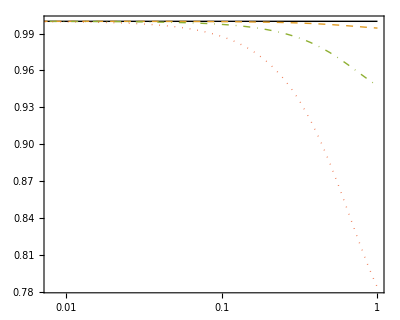

```mathematica
PlotGeff=LogLinearPlot[{1,Geff[a]/.k->300H0/.J̃->10^-2,Geff[a]/.k->300H0/.J̃->10^-1,Geff[a]/.k->300H0/.J̃->0.5}//Evaluate,{a,ai,1},PlotRange->{{8*10^-3,1},All},Frame->True,AspectRatio->0.8,PlotStyle->{Directive[Black,Thick],Directive[Dashed,Thick],Directive[DotDashed,Thick],Directive[Dotted,Thick]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","\\frac{G_\\text{eff}}{G_N}"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda \\text{CDM}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 0.01"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 0.1"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\tilde{J} = 0.5"]},
LegendLayout->{"Row",5},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.25,0.36}]]
```

Solution for the matter contrast on sub-horizon scales

```mathematica
NSolδmΛ=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2 Ωm0/(a^5 Hub[a]^2/H0^2)δm[a]==0,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmSVTDES1=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2/H0^2)δm[a]==0/.k->300H0/.J̃->10^-2,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmSVTDES2=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2/H0^2)δm[a]==0/.k->300H0/.J̃->10^-1,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmSVTDES3=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2/H0^2)δm[a]==0/.k->300H0/.J̃->0.5,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
```

This is a compilation of data for fσ8. You can find it in Sagredo, Nesseris, and Sapone 1806.10822 [astro-ph.CO].

```mathematica
datagrowth=Import["/Users/cosmologygroup/Desktop/PhD_Project/Theoretical_Work/Full_SVT/data_growth_2018_main.txt","Data"];
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Evolution of fσ8

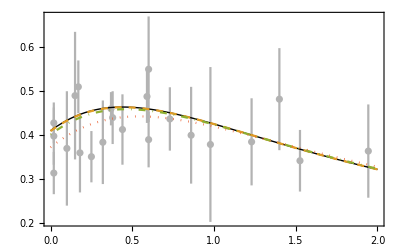

```mathematica
Show[ErrorListPlot[datagrowth,PlotStyle->RGBColor[0.7,0.7,0.7],PlotRange->All],Plot[{σ80 a δm'[a]/δm[1]/.NSolδmΛ,σ80 a δm'[a]/δm[1]/.NSolδmSVTDES1,σ80 a δm'[a]/δm[1]/.NSolδmSVTDES2,σ80 a δm'[a]/δm[1]/.NSolδmSVTDES3}/.a->1/(1+z)//Evaluate,{z,0,2},AspectRatio->1,PlotStyle->{Directive[Black,Thick],Directive[Dashed],Directive[DotDashed],Directive[Dotted]},Frame->True,PlotRange->All],PlotRange->{{0,2},All},Frame->True,Axes->False,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"z","f\\sigma_8"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->13}]
```

```mathematica
Ωm0=.;ΩΛ=.;ai=.;δi=.;σ80=.;
```

## Effective Fluid

### Density, Pressure, Velocity, and Sound Speed

In this case, we do not have anisotropic stress. Therefore, we use the coefficients Y_i instead of the coefficients Z_i

```mathematica
Y1=Simplify[2 D9 H3^2-A5^2 H3^2 κ-B6 D9 H3^2 κ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y2=Simplify[2 F5 H2^2-2 F4 H2 H3-2 D9 F5 H4-2 H3^2 mφ2+D9 F5 H1^2 κ-2 A5 F5 H1 H2 κ-B6 F5 H2^2 κ-A6 D9 H1 H3 κ-D9 F3 H1 H3 κ+A5 F4 H1 H3 κ+A5 A6 H2 H3 κ+A5 F3 H2 H3 κ+B6 F4 H2 H3 κ+A4 D9 H3^2 κ+A5^2 F5 H4 κ+B6 D9 F5 H4 κ+B6 H3^2 mφ2 κ+A5 H3^2 κ μφ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y3=Simplify[2 F5 H4 mφ2+A6 F4 H1 H2 κ-A6 F3 H2^2 κ+A4 F5 H2^2 κ-A4 F4 H2 H3 κ+A6 D9 F3 H4 κ-A5 A6 F4 H4 κ-A4 D9 F5 H4 κ-F5 H1^2 mφ2 κ+A6 H1 H3 mφ2 κ+F3 H1 H3 mφ2 κ-A4 H3^2 mφ2 κ-B6 F5 H4 mφ2 κ+F5 H1 H2 κ μφ-F3 H2 H3 κ μφ-A5 F5 H4 κ μφ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y4=Simplify[-A6 F3 H4 mφ2 κ+A4 F5 H4 mφ2 κ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y5=Simplify[A5^2 H3^2 κ+B6 D9 H3^2 κ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y6=Simplify[-D9 F5 H1^2 κ+2 A5 F5 H1 H2 κ+B6 F5 H2^2 κ+D9 F3 H1 H3 κ-A5 F4 H1 H3 κ-A5 F3 H2 H3 κ-B6 F4 H2 H3 κ-A5^2 F5 H4 κ-B6 D9 F5 H4 κ-B6 H3^2 mφ2 κ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y7=Simplify[F5 H1^2 mφ2 κ-F3 H1 H3 mφ2 κ+B6 F5 H4 mφ2 κ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y8=Simplify[B11 D9 H1 H3-A5 B11 H2 H3-B9 D9 H3^2+3 A5 H3^2 νφ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y9=Simplify[-B11 F4 H1 H2+B11 F3 H2^2-B9 F5 H2^2+B9 F4 H2 H3-B11 D9 F3 H4+A5 B11 F4 H4+B9 D9 F5 H4-B11 H1 H3 mφ2+B9 H3^2 mφ2+3 F5 H1 H2 νφ-3 F3 H2 H3 νφ-3 A5 F5 H4 νφ/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y10=Simplify[B11 F3 H4 mφ2-B9 F5 H4 mφ2/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y11=Simplify[C5 D9 H1 H3-A5 C5 H2 H3+A5 C4 H3^2-C3 D9 H3^2/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y12=Simplify[-C6 D9 F5 H1+A5 C6 F5 H2-C5 F4 H1 H2+C4 F5 H1 H2+C5 F3 H2^2-C3 F5 H2^2+C6 D9 F3 H3-A5 C6 F4 H3-C4 F3 H2 H3+C3 F4 H2 H3-C5 D9 F3 H4+A5 C5 F4 H4-A5 C4 F5 H4+C3 D9 F5 H4-C5 H1 H3 mφ2+C3 H3^2 mφ2/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
Y13=Simplify[C6 F5 H1 mφ2-C6 F3 H3 mφ2+C5 F3 H4 mφ2-C3 F5 H4 mφ2/.κ->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
```

-(512 (Ω_m0/a^3+Ω_Λ)^(3/2) (J̃)^4)/(81 H_0^2 Ω_m0^4)

-(64 (Ω_m0+a^3 Ω_Λ)^(1/4) (11 Ω_m0^2 (a^9 (Ω_m0+a^3 Ω_Λ))^(1/4)+35 Ω_m0 Ω_Λ (a^21 (Ω_m0+a^3 Ω_Λ))^(1/4)+24 Ω_Λ^2 (a^33 (Ω_m0+a^3 Ω_Λ))^(1/4)) (J̃)^4)/(9 a^(39/4) Ω_m0^4)

-(80 H_0^2 (Ω_m0+a^3 Ω_Λ)^(3/2) (13 Ω_m0+16 a^3 Ω_Λ) (29 Ω_m0+20 a^3 Ω_Λ) (J̃)^4)/(9 a^(21/2) Ω_m0^4)

0

(32 √(Ω_m0/a^3+Ω_Λ) (J̃)^3 (3 √2 Ω_m0 √(Ω_m0+a^3 Ω_Λ) (29 Ω_m0+20 a^3 Ω_Λ)+16 a^(3/2) (Ω_m0+a^3 Ω_Λ) J̃))/(81 a^(9/2) H_0^2 Ω_m0^4)

(4 (Ω_m0+a^3 Ω_Λ) (J̃)^3 (7 √2 Ω_m0 (377 Ω_m0^2+724 a^3 Ω_m0 Ω_Λ+320 a^6 Ω_Λ^2)-16 (47 Ω_m0 √(a^3 (Ω_m0+a^3 Ω_Λ))+16 Ω_Λ √(a^9 (Ω_m0+a^3 Ω_Λ))) J̃))/(9 a^9 Ω_m0^4)

0

(32 √(Ω_m0+a^3 Ω_Λ) (13 Ω_m0+4 a^3 Ω_Λ) (29 Ω_m0+20 a^3 Ω_Λ) (J̃)^4)/(27 a^(15/2) Ω_m0^4)

(4 H_0^2 (13 Ω_m0+16 a^3 Ω_Λ) (29 Ω_m0+20 a^3 Ω_Λ) (205 Ω_m0^2+329 a^3 Ω_m0 Ω_Λ+124 a^6 Ω_Λ^2) (J̃)^4)/(9 Ω_m0^4 √(a^21 (Ω_m0+a^3 Ω_Λ)))

0

-(512 (5 Ω_m0^2+7 a^3 Ω_m0 Ω_Λ+2 a^6 Ω_Λ^2) (J̃)^4)/(81 a^6 H_0 Ω_m0^4)

-(128 H_0 (129 Ω_m0^3+328 a^3 Ω_m0^2 Ω_Λ+263 a^6 Ω_m0 Ω_Λ^2+64 a^9 Ω_Λ^3) (J̃)^4)/(9 a^9 Ω_m0^4)

0

#### Density perturbation

```mathematica
SNSδρDE=Simplify[-(k^6/ah[]^6 Y1+k^4/ah[]^4 Y2+k^2/ah[]^2 Y3+Y4)/(k^6/ah[]^6 Y5+k^4/ah[]^4 Y6+k^2/ah[]^2 Y7)*δρm/.ah[]->a/.δρm->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
%/.J̃->0 (* ΛCDM Limit *)
```

(4 √a (Ω_m0+a^3 Ω_Λ)^(3/2) (32 a^2 k^4+396 a H_0^2 k^2 Ω_m0+16965 H_0^4 Ω_m0^2+864 a^4 H_0^2 k^2 Ω_Λ+32580 a^3 H_0^4 Ω_m0 Ω_Λ+14400 a^6 H_0^4 Ω_Λ^2) J̃)/(k^2 (3 √2 Ω_m0 (8 a k^2+273 H_0^2 Ω_m0+336 a^3 H_0^2 Ω_Λ) (29 Ω_m0^2+49 a^3 Ω_m0 Ω_Λ+20 a^6 Ω_Λ^2)+16 (8 a^7 k^2 Ω_Λ √(Ω_m0/a^3+Ω_Λ)+8 k^2 Ω_m0 √(a^5 (Ω_m0+a^3 Ω_Λ))-9 H_0^2 (47 Ω_m0^2 √(a^3 (Ω_m0+a^3 Ω_Λ))+63 Ω_m0 Ω_Λ √(a^9 (Ω_m0+a^3 Ω_Λ))+16 Ω_Λ^2 √(a^15 (Ω_m0+a^3 Ω_Λ)))) J̃))

0

Simplification for small  J̃

```mathematica
SNSδρDEJ=FullSimplify[Series[SNSδρDE,{J̃,0,1}]//Normal,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
```

(2 √2 √(a (Ω_m0+a^3 Ω_Λ)) ((28 a)/(29 Ω_m0+20 a^3 Ω_Λ)+3 H_0^2 (5/k^2-(96 a)/(8 a k^2+273 H_0^2 Ω_m0+336 a^3 H_0^2 Ω_Λ))) J̃)/(21 Ω_m0)

Simplification for large k

```mathematica
Series[SNSδρDEJ,{k,∞,2}]
```

(8 √2 a √(a (Ω_m0+a^3 Ω_Λ)) J̃)/(3 Ω_m0 (29 Ω_m0+20 a^3 Ω_Λ))-(2 (√2 H_0^2 √(a (Ω_m0+a^3 Ω_Λ)) J̃))/(Ω_m0 k^2)+O[1/k]^3

#### Pressure perturbation

```mathematica
SNSδpDE=Simplify[1/3(k^4/ah[]^4 Y8+k^2/ah[]^2 Y9+Y10)/(k^6/ah[]^6 Y5+k^4/ah[]^4 Y6+k^2/ah[]^2 Y7)*δρm/.ah[]->a/.δρm->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
%/.J̃->0 (* ΛCDM Limit *)
```

(H_0^2 √(a (Ω_m0+a^3 Ω_Λ)) (29 Ω_m0+20 a^3 Ω_Λ) (104 a k^2 Ω_m0+7995 H_0^2 Ω_m0^2+32 a^4 k^2 Ω_Λ+14676 a^3 H_0^2 Ω_m0 Ω_Λ+5952 a^6 H_0^2 Ω_Λ^2) J̃)/(k^2 (3 √2 Ω_m0 (8 a k^2+273 H_0^2 Ω_m0+336 a^3 H_0^2 Ω_Λ) (29 Ω_m0^2+49 a^3 Ω_m0 Ω_Λ+20 a^6 Ω_Λ^2)+16 (8 a^7 k^2 Ω_Λ √(Ω_m0/a^3+Ω_Λ)+8 k^2 Ω_m0 √(a^5 (Ω_m0+a^3 Ω_Λ))-9 H_0^2 (47 Ω_m0^2 √(a^3 (Ω_m0+a^3 Ω_Λ))+63 Ω_m0 Ω_Λ √(a^9 (Ω_m0+a^3 Ω_Λ))+16 Ω_Λ^2 √(a^15 (Ω_m0+a^3 Ω_Λ)))) J̃))

0

Simplification for small  J̃

```mathematica
SNSδpDEJ=FullSimplify[Series[SNSδpDE,{J̃,0,1}]//Normal,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
```

(a H_0^2 (13 Ω_m0 (8 a k^2+615 H_0^2 Ω_m0)+4 a^3 (8 a k^2+3669 H_0^2 Ω_m0) Ω_Λ+5952 a^6 H_0^2 Ω_Λ^2) J̃)/(3 √2 k^2 Ω_m0 √(a (Ω_m0+a^3 Ω_Λ)) (8 a k^2+273 H_0^2 Ω_m0+336 a^3 H_0^2 Ω_Λ))

#### Velocity perturbation

```mathematica
SNSVDE=k^2/a*Simplify[(k^4/ah[]^4 Y11+k^2/ah[]^2 Y12+Y13)/(k^6/ah[]^6 Y5+k^4/ah[]^4 Y6+k^2/ah[]^2 Y7)*δρm/.ah[]->a/.δρm->1,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
%/.J̃->0 (* ΛCDM Limit *)
```

-((32 a H_0 (Ω_m0+a^3 Ω_Λ) (20 a k^2 Ω_m0+1161 H_0^2 Ω_m0^2+8 a^4 k^2 Ω_Λ+1791 a^3 H_0^2 Ω_m0 Ω_Λ+576 a^6 H_0^2 Ω_Λ^2) J̃)/(3 √2 Ω_m0 (8 a k^2+273 H_0^2 Ω_m0+336 a^3 H_0^2 Ω_Λ) (29 Ω_m0^2+49 a^3 Ω_m0 Ω_Λ+20 a^6 Ω_Λ^2)+16 (8 a^7 k^2 Ω_Λ √(Ω_m0/a^3+Ω_Λ)+8 k^2 Ω_m0 √(a^5 (Ω_m0+a^3 Ω_Λ))-9 H_0^2 (47 Ω_m0^2 √(a^3 (Ω_m0+a^3 Ω_Λ))+63 Ω_m0 Ω_Λ √(a^9 (Ω_m0+a^3 Ω_Λ))+16 Ω_Λ^2 √(a^15 (Ω_m0+a^3 Ω_Λ)))) J̃))

0

Simplification for small  J̃

```mathematica
SNSVDEJ=FullSimplify[Series[SNSVDE,{J̃,0,1}]//Normal,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
```

-(16 √2 a H_0 (Ω_m0 (20 a k^2+1161 H_0^2 Ω_m0)+a^3 (8 a k^2+1791 H_0^2 Ω_m0) Ω_Λ+576 a^6 H_0^2 Ω_Λ^2) J̃)/(3 Ω_m0 (29 Ω_m0+20 a^3 Ω_Λ) (8 a k^2+273 H_0^2 Ω_m0+336 a^3 H_0^2 Ω_Λ))

Simplification for large k

```mathematica
Series[SNSVDEJ,{k,∞,2}]
```

-(2 (√2 H_0 (20 a Ω_m0+8 a^4 Ω_Λ) J̃))/(3 (Ω_m0 (29 Ω_m0+20 a^3 Ω_Λ)))-(√2 H_0^3 (11 Ω_m0+8 a^3 Ω_Λ) J̃)/(Ω_m0 k^2)+O[1/k]^3

#### Sound Speed

```mathematica
cs2DE=FullSimplify[SNSδpDE/SNSδρDE,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]
```

(H_0^2 (29 Ω_m0+20 a^3 Ω_Λ) (13 Ω_m0 (8 a k^2+615 H_0^2 Ω_m0)+4 a^3 (8 a k^2+3669 H_0^2 Ω_m0) Ω_Λ+5952 a^6 H_0^2 Ω_Λ^2))/(4 (Ω_m0+a^3 Ω_Λ) (32 a^2 k^4+396 a H_0^2 k^2 Ω_m0+16965 H_0^4 Ω_m0^2+36 a^3 H_0^2 (24 a k^2+905 H_0^2 Ω_m0) Ω_Λ+14400 a^6 H_0^4 Ω_Λ^2))

This is the sound speed. Note that it does not depend on J but it does depend on the scale.

At early times, the sound speed tends to a constant superluminal value

```mathematica
Simplify[Series[cs2DE,{a,0,0}]//Normal,Assumptions->H0>0&&Ωm0>0&&ΩΛ>0&&a>0&&J̃>0]//N
```

3.41667

Plot of the analytical sound speed for several values of k

```mathematica
Subscript[Ω, Λ]=0.7;Subscript[Ω, m0]=0.3;k=.;
```

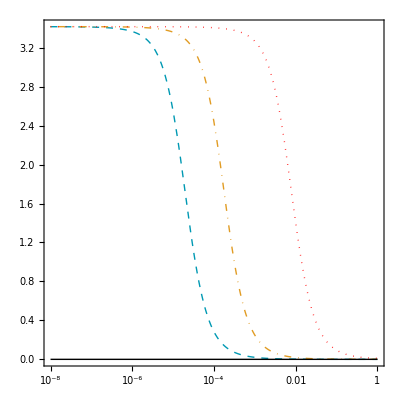

```mathematica
LogLinearPlot[{cs2DE/.k->600H0,cs2DE/.k->200H0,cs2DE/.k->30H0,0}//Evaluate,{a,10^-8,1},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,
PlotStyle->{Directive[RGBColor[0,0.6,0.7],Dashed,Thick],Directive[DotDashed,Thick],Directive[Red,Dotted,Thick],Directive[Black,Thick]},BaseStyle->{FontFamily->"Times",FontSize->13},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","c_{s, \\text{DE}}^2"},RotateLabel->False,FrameStyle->BlackFrame,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["k = 600 H_0"],(MaTeX[#,Magnification->1.2]&)/@Style["k = 200 H_0"],
(MaTeX[#,Magnification->1.2]&)/@Style["k = 30 H_0"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->None],
{0.23,0.2}]]
```

This is one of the plots in the paper.

```mathematica
LabeledTicks=Table[{10^i,10^i//N},{i,-5,1}];
UnlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,LabeledTicks[[All,1]]}],1];
MyTicks=Join[LabeledTicks,UnlabeledTicks];
```

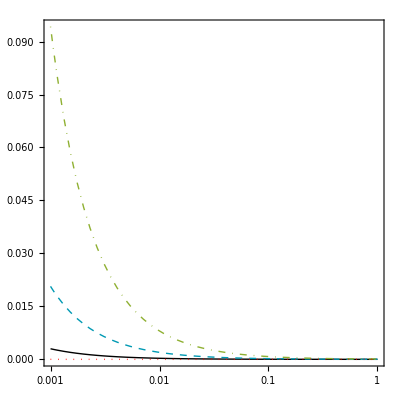

```mathematica
LogLinearPlot[{3*10^-6*a^-1,cs2DE/.k->600H0,cs2DE/.k->300H0,0},{a,10^-3,1},Frame->True,Axes->False,AspectRatio->1,PlotRange->{{10^-3,1},All},
PlotStyle->{Directive[Black,Thick],Directive[RGBColor[0,0.6,0.7],Dashed,Thick],Directive[DotDashed,Thick],Directive[Red,Dotted,Thick]},BaseStyle->{FontFamily->"Times",FontSize->13},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","c_{s, \\text{DE}}^2"},RotateLabel->False,FrameStyle->BlackFrame,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Eq. } (5.31)"],(MaTeX[#,Magnification->1.2]&)/@Style["k = 600 H_0"],
(MaTeX[#,Magnification->1.2]&)/@Style["k = 300 H_0"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.71,0.75}],FrameTicks->{{Automatic,None},{MyTicks,None}}]
```

```mathematica
Subscript[Ω, Λ]=.;Subscript[Ω, m0]=.;
```

### Evolution of Matter and Dark Energy Perturbations

```mathematica
δ0=1; (* Overall Scale *)
Ωm0=0.3; (* Matter Today *)
ΩΛ=0.7; (* Dark Energy Today *)
k=300H0; (* Momentum *)
H0=1;
```

```mathematica
ai=10^-3; (* Initial Scale Factor -> Deep in the matter epoch *)
δmi=δ0*ai(1+3*(Hub[ai]^2*ai^2)/k^2); (* Initial Condition for δm *)
δmM[a_]=δ0*a(1+3*(Hub[a]^2*a^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2); (* Initial Condition for Vm *)
VmM[a_]=-δ0*H0*√Ωm0*a^(1/2);
Φi=-3/2 δ0*H0^2*Ωm0/k^2; (* Potential during Matter Domination *)
```

Functions

```mathematica
Hub[a_]=H0 √(Ωm0*a^-3+ΩΛ);  (* Hubble Parameter in ΛCDM *)
Φ[a_]=-3/2 H0^2/(a*k^2)(Ωm0(δm[a]+(3a*Hub[a])/k^2*Vm[a])+ΩΛ*a^(-3wDE)(δDEA[a]+(3a*Hub[a])/k^2*VDEA[a]));  (* Total Potential *)
δDEA[a_]=SNSδρDE(Ωm0*a^-3)/(ρDE/(3 H0^2))*δm[a];
VDEA[a_]=SNSVDE(Ωm0*a^-3)/(ρDE/(3 H0^2))*δm[a];
```

Evolution Equations for Matter

```mathematica
Eqδm[a_]=-δm'[a]-Vm[a]/(a^2*Hub[a])+3Φ'[a];
EqVm[a_]=-Vm'[a]-Vm[a]/a+k^2/(a^2*Hub[a])Φ[a];
```

```mathematica
SolPertsI=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.J̃->10^-2,{δm,Vm},{a,ai,1}][[1]]
```

{δ_m→InterpolatingFunction[…],V_m→InterpolatingFunction[…]}

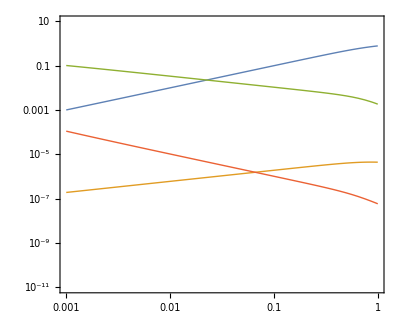

```mathematica
LogLogPlot[{{δm[a],1/k^2 Vm[a],δDEA[a],1/k^2 VDEA[a]}/.J̃->10^-2/.SolPertsI}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->{10^-11,10},AspectRatio->0.8,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Directive[Thick],Directive[Thick],Directive[Thick],Directive[Thick]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_m"],(MaTeX[#,Magnification->1.4]&)/@Style["\\frac{V_m}{k^2}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_\\text{DE}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\frac{V_\\text{DE}}{k^2}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.5,0.15}],FrameTicks->{{Automatic,None},{MyTicks,None}}]
```

Difference between the analytical solution for the matter contrast in matter domination and the numerical solution.

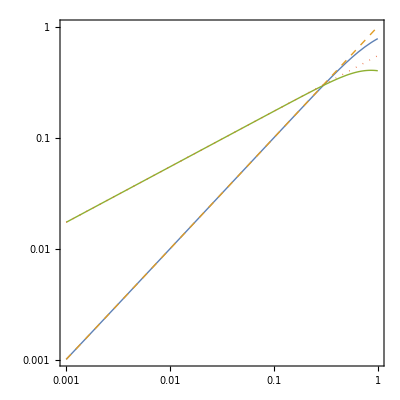

```mathematica
LogLogPlot[{{δm[a],δmM[a],Vm[a],VmM[a]}/.SolPertsI}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->Automatic,AspectRatio->1,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick],Directive[Dashed,Thick],Directive[Thick],Directive[Dotted,Thick]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_m"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_m^\\text{(th)}"],
(MaTeX[#,Magnification->1.4]&)/@Style["V_m"],
(MaTeX[#,Magnification->1.4]&)/@Style["V_m^\\text{(th)}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.84,0.23}]]
```

```mathematica
{δm[ai],1/k^2 Vm[ai],δDEA[ai],1/k^2 VDEA[ai]}/.J̃->10^-2/.SolPertsI
```

{0.00101,-1.9245×10^-7,0.101851,-0.000111705}

```mathematica
SolPertsII=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.J̃->0.1,{δm,Vm},{a,ai,1}][[1]]
```

{δ_m→InterpolatingFunction[…],V_m→InterpolatingFunction[…]}

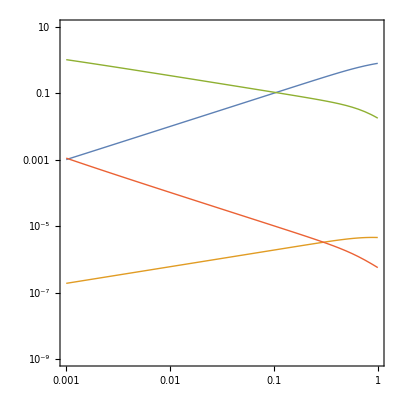

```mathematica
LogLogPlot[{{δm[a],1/k^2 Vm[a],δDEA[a],1/k^2 VDEA[a]}/.J̃->0.1/.SolPertsII}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->{10^-9,10},AspectRatio->1,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick],Directive[Thick],Directive[Thick],Directive[Thick]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_m"],(MaTeX[#,Magnification->1.4]&)/@Style["\\frac{V_m}{k^2}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_\\text{DE}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\frac{V_\\text{DE}}{k^2}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.5,0.12}],FrameTicks->{{Automatic,None},{MyTicks,None}}]
```

```mathematica
{δm[ai],1/k^2 Vm[ai],δDEA[ai],1/k^2 VDEA[ai]}/.J̃->0.1/.SolPertsII
```

{0.00101,-1.9245×10^-7,1.01851,-0.00111704}

```mathematica
SolPertsIII=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.J̃->0.5,{δm,Vm},{a,ai,1}][[1]]
```

{δ_m→InterpolatingFunction[…],V_m→InterpolatingFunction[…]}

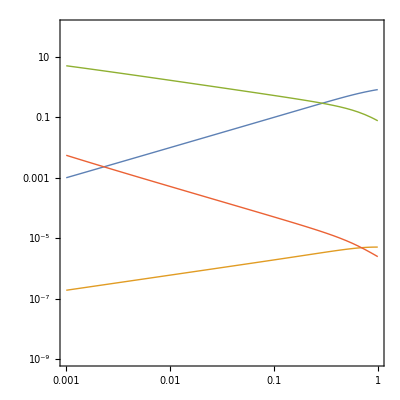

```mathematica
LogLogPlot[{{δm[a],1/k^2 Vm[a],δDEA[a],1/k^2 VDEA[a]}/.J̃->0.5/.SolPertsIII}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->{10^-9,100},AspectRatio->1,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick],Directive[Thick],Directive[Thick],Directive[Thick]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_m"],(MaTeX[#,Magnification->1.4]&)/@Style["\\frac{V_m}{k^2}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\delta_\\text{DE}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\frac{V_\\text{DE}}{k^2}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.5,0.12}],FrameTicks->{{Automatic,None},{MyTicks,None}}]
```

```mathematica
{δm[ai],1/k^2 Vm[ai],δDEA[ai],1/k^2 VDEA[ai]}/.J̃->0.5/.SolPertsIII
```

{0.00101,-1.9245×10^-7,5.09251,-0.00558518}

Change of DE perturbations wrt J̃

```mathematica
δ0=.;H0=.;Ωm0=.;ΩΛ=.;k=.;
```

## CMB Angular and Matter Power Spectra

This retrieves the first and second columns of the data generated by solving perturbations in SVTDES and ΛCDM using CLASS. Figures in the paper are different to these ones. You should replace the location of your files here:

```mathematica
dataPk1=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES00_pk.dat",{"Data",{All},{1,2}}];
dataPk2=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES01_pk.dat",{"Data",{All},{1,2}}];
dataPk3=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES02_pk.dat",{"Data",{All},{1,2}}];
dataPkΛCDM=Import["/Users/cosmologygroup/EFCLASS/output/base_2018_plikHM_TTTEEE_lowl_lowE_lensing00_pk.dat",{"Data",{All},{1,2}}];
```

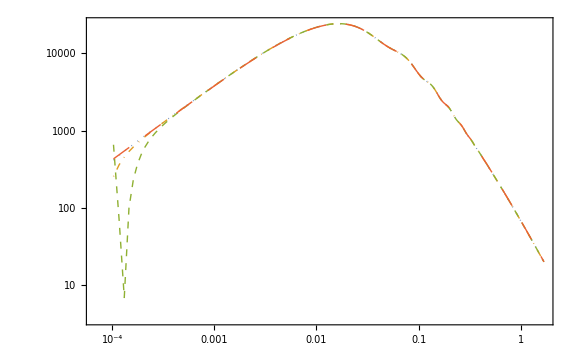

```mathematica
MatterSpectrum=ListLogLogPlot[{dataPk1,dataPk2,dataPk3,dataPkΛCDM},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\left[ h \\text{Mpc}^{-1} \\right]","P(k) \\left[ (h^{-1} \\text{Mpc})^3 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-4}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-3}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-2}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.5,0.25}],ImageSize->Large]
```

This retrieves the first and second columns of the data generated by solving perturbations in SVTDES and ΛCDM using CLASS. You can select another column, for instance {1, 3} for plotting the EE polarization of CMB. You should replace the location of your files here:

```mathematica
dataClTT1=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES00_cl.dat",{"Data",{All},{1,2}}];
dataClTT2=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES01_cl.dat",{"Data",{All},{1,2}}];
dataClTT3=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES02_cl.dat",{"Data",{All},{1,2}}];
dataClTTΛCDM=Import["/Users/cosmologygroup/EFCLASS/output/base_2018_plikHM_TTTEEE_lowl_lowE_lensing00_cl.dat",{"Data",{All},{1,2}}];
```

Import::noelem: The Import element "2" is not present when importing as Table.

This is necessary in order to get the right units.

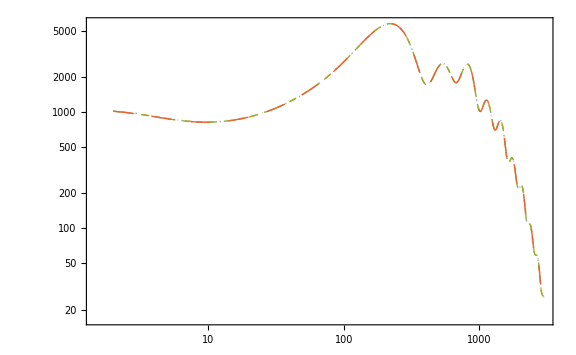

```mathematica
ClTT1={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTT1; 
ClTT2={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTT2; 
ClTT3={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTT3; 
ClTTΛCDM={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTΛCDM;
TTSpectrum=ListLogLogPlot[{ClTT1,ClTT2,ClTT3,ClTTΛCDM},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{TT} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-4}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-3}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-2}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.5,0.25}],ImageSize->Large]
```

Maybe is more common to see this plot in this scale:

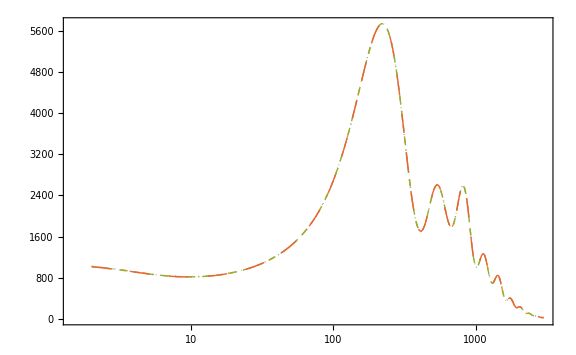

```mathematica
TTLinearSpectrum=ListLogLinearPlot[{ClTT1,ClTT2,ClTT3,ClTTΛCDM},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{TT} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-4}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-3}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-2}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.15,0.77}],ImageSize->Large]
```

```mathematica
dataClEE1=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES00_cl.dat",{"Data",{All},{1,3}}];
dataClEE2=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES01_cl.dat",{"Data",{All},{1,3}}];
dataClEE3=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES02_cl.dat",{"Data",{All},{1,3}}];
dataClEEΛCDM=Import["/Users/cosmologygroup/EFCLASS/output/base_2018_plikHM_TTTEEE_lowl_lowE_lensing00_cl.dat",{"Data",{All},{1,3}}];
```

Import::noelem: The Import element "3" is not present when importing as Table.

This is necessary in order to get the right units.

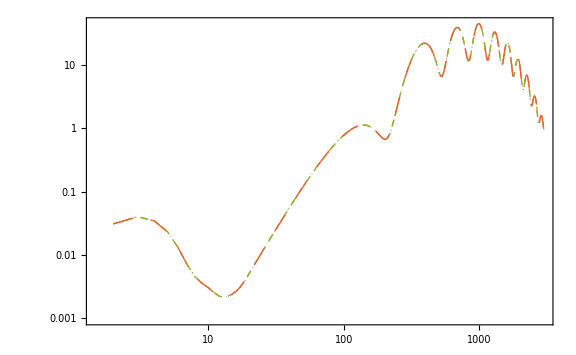

```mathematica
ClEE1={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEE1; 
ClEE2={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEE2; 
ClEE3={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEE3; 
ClEEΛCDM={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEEΛCDM;
EESpectrum=ListLogLogPlot[{ClEE1,ClEE2,ClEE3,ClEEΛCDM},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{EE} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-4}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-3}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-2}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.84,0.25}],ImageSize->Large]
```

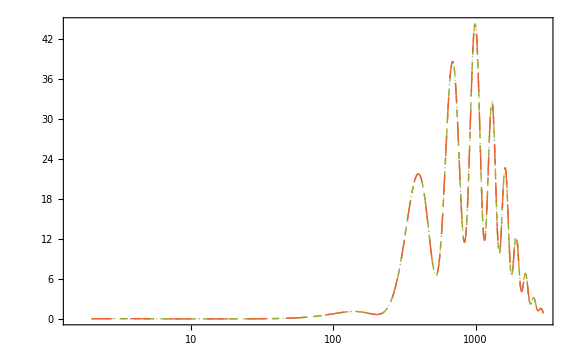

```mathematica
EELinearSpectrum=ListLogLinearPlot[{ClEE1,ClEE2,ClEE3,ClEEΛCDM},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{EE} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-4}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-3}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-2}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.2,0.25}],ImageSize->Large]
```

```mathematica
dataClTE1=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES00_cl.dat",{"Data",{All},{1,4}}];
dataClTE2=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES01_cl.dat",{"Data",{All},{1,4}}];
dataClTE3=Import["/Users/cosmologygroup/EFCLASS/output/SVTDES02_cl.dat",{"Data",{All},{1,4}}];
dataClTEΛCDM=Import["/Users/cosmologygroup/EFCLASS/output/base_2018_plikHM_TTTEEE_lowl_lowE_lensing00_cl.dat",{"Data",{All},{1,4}}];
```

Import::noelem: The Import element "4" is not present when importing as Table.

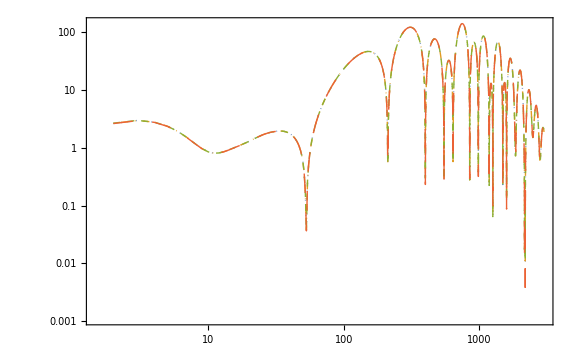

```mathematica
ClTE1={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTE1; 
ClTE2={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTE2; 
ClTE3={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTE3; 
ClTEΛCDM={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTEΛCDM;
TESpectrum=ListLogLogPlot[{ClTE1,ClTE2,ClTE3,ClTEΛCDM},Joined->True,PlotRange->Full,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{TE} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-4}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-3}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-2}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.2,0.25}],ImageSize->Large]
```

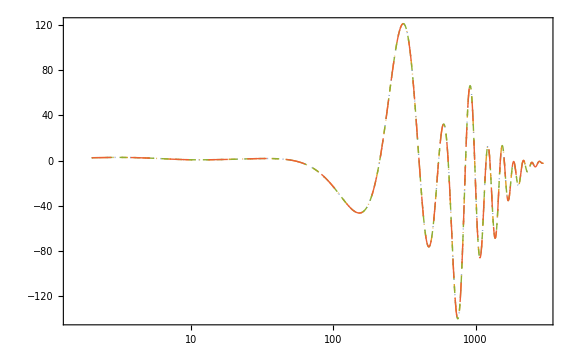

```mathematica
ClTE1={#[[1]],#[[2]]*(2.7255*10^6)^2}&/@dataClTE1; 
ClTE2={#[[1]],#[[2]]*(2.7255*10^6)^2}&/@dataClTE2; 
ClTE3={#[[1]],#[[2]]*(2.7255*10^6)^2}&/@dataClTE3; 
ClTEΛCDM={#[[1]],#[[2]]*(2.7255*10^6)^2}&/@dataClTEΛCDM;
TELinearSpectrum=ListLogLinearPlot[{ClTE1,ClTE2,ClTE3,ClTEΛCDM},Joined->True,PlotRange->Full,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{TE} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-4}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-3}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\tilde{J} = 10^{-2}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.2,0.25}],ImageSize->Large]
```

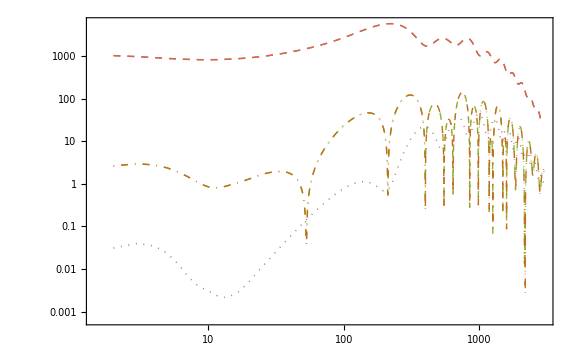

```mathematica
SVTDESTT={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTT1;
SVTDESEE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEE1; 
SVTDESTE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTE1;
ΛCDMTT={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTΛCDM;
ΛCDMEE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEEΛCDM; 
ΛCDMTE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTEΛCDM;
BBSpectrum=ListLogLogPlot[{SVTDESTT,SVTDESEE,SVTDESTE,ΛCDMTT,ΛCDMEE,ΛCDMTE},Joined->True,PlotRange->Full,Frame->True,FrameStyle->BlackFrame,PlotLabel->(MaTeX["\\textbf{SVTDES}",Magnification->18/12]),FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dashed],Directive[Thick,Dotted],Directive[Thick,DotDashed]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["TT"],(MaTeX[#,Magnification->1.4]&)/@Style["EE"],(MaTeX[#,Magnification->1.4]&)/@Style["TE"],(MaTeX[#,Magnification->1.4]&)/@Style["TT"],(MaTeX[#,Magnification->1.4]&)/@Style["EE"],(MaTeX[#,Magnification->1.4]&)/@Style["TE"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,1},LegendFunction->Frame],
{0.68,0.12}],ImageSize->Large]
```